## Cross sections and plots associated with the paper “Polarized J/ψ production in SIDIS at large Q^2: Comparing quark fragmentation and photon gluon fusion” by Marston Copeland, Sean Fleming, Rohit Gupta, Reed Hodges, and Thomas Mehen

## Contact: reed.hodges@duke.edu

```mathematica
<<MaTeX`
SetOptions[Plot,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameStyle->Black];
SetOptions[MaTeX,Magnification->1.5];
```

## PDF data

## Data tables

These are evaluated at Q = 30 GeV

### gluon NNPDF

This is data used for interpolation, from pdfFunction[5,0,x,Q=30] in ManeParse for NNPDF31_nnlo_as_0118.  x∈[0.01,1.0] for 500 points

```mathematica
gPDFdata={{0.01,753.7728104866009},{0.011980000000000001,564.9235026890851},{0.01396,440.76162814300756},{0.01594,354.69107592792886},{0.01792,291.79456613582465},{0.0199,244.7482543201847},{0.02188,208.12863628698685},{0.02386,179.2646080383151},{0.025840000000000002,156.10665727001094},{0.027819999999999998,136.99178520523026},{0.0298,121.18854094027998},{0.03178,107.98208936283646},{0.03376,96.7592195213571},{0.03574,87.10154323659171},{0.037720000000000004,78.79514494003884},{0.0397,71.60466144987646},{0.04168,65.33945310635615},{0.043660000000000004,59.77999563177123},{0.04564,54.85675607654965},{0.04762,50.49305262625236},{0.0496,46.61030623303888},{0.05158,43.142003495809604},{0.05356,40.03146645291061},{0.05554,37.192808081888224},{0.05752,34.618363955786386},{0.059500000000000004,32.28446725725897},{0.06148,30.163803896343534},{0.06346,28.232468664144474},{0.06544,26.469449524969942},{0.06742,24.856202780753115},{0.0694,23.37179568827298},{0.07138,21.988124234227044},{0.07336,20.712218726493326},{0.07533999999999999,19.533953399072},{0.07732,18.444239682894416},{0.0793,17.4348967196993},{0.08127999999999999,16.49854080178429},{0.08326,15.628490587108825},{0.08524,14.818685524680726},{0.08721999999999999,14.063615390999857},{0.08919999999999999,13.355902685747143},{0.09118,12.691028325811548},{0.09315999999999999,12.068866616027714},{0.09513999999999999,11.48602983625382},{0.09712,10.939406530181678},{0.0991,10.426133906830671},{0.10107999999999999,9.942720761245868},{0.10306,9.487040073206602},{0.10504,9.057802209903132},{0.10701999999999999,8.65314514510988},{0.109,8.271342148451781},{0.11098,7.910789716302487},{0.11295999999999999,7.569719225853969},{0.11494,7.246670947658803},{0.11692,6.940869859474091},{0.11889999999999999,6.65120388678843},{0.12088,6.376633817682492},{0.12286,6.1161874315962335},{0.12483999999999999,5.868844396113132},{0.12682,5.633578480824157},{0.1288,5.4099649460221615},{0.13078,5.197310959456199},{0.13276,4.994965020838478},{0.13474,4.8023139249849445},{0.13672,4.6187490267093345},{0.13870000000000002,4.443538686629012},{0.14068,4.276439160225211},{0.14266,4.1170027984696205},{0.14464000000000002,3.9648064640893623},{0.14662,3.8194498764968703},{0.1486,3.6805540890362924},{0.15058000000000002,3.5476082491401977},{0.15256,3.4204483339609397},{0.15454,3.2987790342493644},{0.15652000000000002,3.182316208866656},{0.1585,3.0707899147675013},{0.16048,2.963943531120679},{0.16246000000000002,2.861437810664005},{0.16444,2.7631338621879427},{0.16642,2.6688474778718865},{0.1684,2.5783843720666275},{0.17038,2.4915592903610158},{0.17236,2.408195490846437},{0.17434,2.328080267079337},{0.17632,2.251084767781965},{0.17830000000000001,2.177084926412327},{0.18028,2.105942855277433},{0.18226,2.0375266585120535},{0.18424000000000001,1.971710110112299},{0.18622,1.908340843687118},{0.1882,1.847314466305403},{0.19018000000000002,1.7885552052332905},{0.19216,1.7319651513519183},{0.19414,1.6774503897745285},{0.19612000000000002,1.62492079822044},{0.1981,1.5742767493956906},{0.20008,1.5254316501122158},{0.20206000000000002,1.478329967773171},{0.20404,1.43289975372108},{0.20602,1.3890718252113239},{0.20800000000000002,1.3467796337653317},{0.20998,1.305952887608206},{0.21196,1.2665201479588142},{0.21394000000000002,1.228443207835454},{0.21592,1.1916684258960422},{0.2179,1.1561441104975736},{0.21988000000000002,1.1218204319117808},{0.22186,1.0886465361338924},{0.22384,1.0565594771787767},{0.22582000000000002,1.0255383946897532},{0.2278,0.9955436094009847},{0.22978,0.9665368097017172},{0.23176000000000002,0.9384809932147036},{0.23374,0.91134041134394},{0.23572,0.8850734986450097},{0.2377,0.859654967680113},{0.23968,0.8350538102911176},{0.24166,0.8112398757538503},{0.24364,0.7881839934530509},{0.24562,0.7658579333779396},{0.24760000000000001,0.7442216586432754},{0.24958,0.7232611340949134},{0.25156,0.7029556757755544},{0.25354,0.6832827555934244},{0.25551999999999997,0.6642205437288486},{0.2575,0.6457478817880612},{0.25948,0.6278421792211409},{0.26146,0.6104850628258661},{0.26344,0.5936586444447686},{0.26542,0.5773446598948252},{0.2674,0.5615253859516125},{0.26938,0.5461836204685073},{0.27136,0.5312973689026672},{0.27334,0.5168523232217059},{0.27532,0.5028386013964312},{0.2773,0.4892423595150957},{0.27928000000000003,0.4760501462604136},{0.28126,0.46324888909072703},{0.28324,0.45082606309670015},{0.28522000000000003,0.4387693618574883},{0.2872,0.42706643737691585},{0.28918,0.41570553750937},{0.29116000000000003,0.40467522978568177},{0.29314,0.3939643906169309},{0.29512,0.38355874400375106},{0.29710000000000003,0.37344242459100185},{0.29908,0.3636167036375834},{0.30106,0.35407357031536996},{0.30304000000000003,0.34480522316053985},{0.30502,0.33580406327826273},{0.307,0.32706376069662535},{0.30898000000000003,0.3185833052931227},{0.31096,0.310346745307438},{0.31294,0.30234589750949087},{0.31492000000000003,0.29457278447125285},{0.3169,0.2870196281374637},{0.31888,0.2796788436358706},{0.32086000000000003,0.2725348522423763},{0.32284,0.2655898787202067},{0.32482,0.25883837123198183},{0.3268,0.25227474722654414},{0.32878,0.2458935586311261},{0.33076,0.23968948782626925},{0.33274,0.233656650407821},{0.33472,0.227790655563584},{0.3367,0.222086822129644},{0.33868,0.21654044416096893},{0.34066,0.2111469251209828},{0.34264,0.20590177472039498},{0.34462,0.20079961916036965},{0.3466,0.19583689323678927},{0.34858,0.19101006991734046},{0.35056,0.1863152723881801},{0.35254,0.18174871093016534},{0.35452,0.17730668048672737},{0.3565,0.1729850333482829},{0.35848,0.16878041778155356},{0.36046,0.16468994615602556},{0.36244,0.16071037507972216},{0.36442,0.15683853164983996},{0.3664,0.1530713115481559},{0.36838,0.1494051038697613},{0.37036,0.14583679091458554},{0.37234,0.14236450686882945},{0.37432,0.13898561839460485},{0.3763,0.1356975475779835},{0.37828,0.13249777047849162},{0.38026,0.12938384308913306},{0.38224,0.12635338676804858},{0.38422,0.12340394092901825},{0.3862,0.12053316820228542},{0.38818,0.11773877890722852},{0.39016,0.11501852984228741},{0.39214,0.11236995514272487},{0.39412,0.10978939002433659},{0.3961,0.1072769023248204},{0.39808,0.1048307525442463},{0.40006,0.10244923561961734},{0.40204,0.1001306800768806},{0.40402,0.09787344720787194},{0.406,0.09567755558442963},{0.40798,0.09353955364760805},{0.40996,0.09145760372630125},{0.41194000000000003,0.08942993224628026},{0.41392,0.08745479956911999},{0.4159,0.08553049918439799},{0.41788000000000003,0.0836524328402925},{0.41986,0.08182181794269455},{0.42184,0.08003816293881706},{0.42382000000000003,0.07830042742288744},{0.4258,0.07660759034097381},{0.42778,0.07495864954313021},{0.42976000000000003,0.0733554055093873},{0.43174,0.07179484946754716},{0.43372,0.07027417883786494},{0.43570000000000003,0.06879184399958584},{0.43768,0.0673463233729815},{0.43966,0.06593612278793866},{0.44164000000000003,0.06455666322824019},{0.44362,0.06320765133566249},{0.4456,0.06189106541726461},{0.44758000000000003,0.06060638251756639},{0.44956,0.05935308889411254},{0.45154,0.058130679815477086},{0.45352000000000003,0.05694126977351799},{0.4555,0.055785003466440566},{0.45748,0.05465669410272258},{0.45946,0.053554892860684385},{0.46144,0.05247817578573125},{0.46342,0.05142514325912033},{0.4654,0.05039272038175159},{0.46738,0.04937702539345922},{0.46936,0.04838226864849781},{0.47134,0.04740811532553852},{0.47332,0.04645423620577284},{0.4753,0.04552030755621808},{0.47728,0.044606385977556874},{0.47926,0.04371421987272087},{0.48124,0.04284051946712914},{0.48322,0.04198452739695052},{0.4852,0.041145498660929154},{0.48718,0.04032270036916428},{0.48916,0.039515411497991114},{0.49114,0.03872608331241859},{0.49312,0.03795036629317229},{0.4951,0.03718701191635084},{0.49708,0.03643483951242571},{0.49906,0.03569268714889937},{0.5010399999999999,0.03495941126008209},{0.50302,0.03422437801499768},{0.505,0.03349579744136656},{0.50698,0.03277618833527114},{0.50896,0.03206624440594185},{0.5109400000000001,0.031366648609532206},{0.51292,0.030678073356666828},{0.5149,0.030017785668314683},{0.51688,0.029374197160824428},{0.51886,0.028736978803918792},{0.52084,0.02810306116309385},{0.52282,0.027469421301533698},{0.5248,0.02683308190296278},{0.52678,0.026174482509557014},{0.52876,0.025496966748335122},{0.53074,0.02481567741170356},{0.53272,0.024132453705693186},{0.5347,0.02344910759393395},{0.53668,0.022767424300188535},{0.53866,0.02208866672192654},{0.54064,0.021414453816851812},{0.54262,0.020747380032887373},{0.5446,0.020089314204858957},{0.54658,0.019442098087984874},{0.54856,0.01880754684658846},{0.55054,0.018190542476179794},{0.55252,0.01759736130756049},{0.5545,0.01701977587908701},{0.55648,0.016457737138799854},{0.55846,0.01591119673038742},{0.56044,0.015380106980897541},{0.56242,0.014864683339550743},{0.5644,0.01436628611630514},{0.56638,0.013882827148090457},{0.56836,0.013413947990302558},{0.57034,0.012959295175861689},{0.57232,0.01251852012911119},{0.5743,0.012091279081497371},{0.57628,0.011677344676696115},{0.57826,0.01127625331275064},{0.58024,0.010887655583844193},{0.58222,0.010511208248378432},{0.5842,0.010146572718081689},{0.58618,0.009793414979418978},{0.58816,0.009451304160623232},{0.59014,0.00912001473284586},{0.59212,0.00879926405901444},{0.5941,0.008488754550209499},{0.59608,0.008188192571518118},{0.59806,0.00789728837658127},{0.60004,0.0076156813447713564},{0.60202,0.007343144660019023},{0.604,0.007079448806410365},{0.60598,0.006824335633444247},{0.6079600000000001,0.006577550353590718},{0.60994,0.006338841487706329},{0.61192,0.006107882106601885},{0.6139,0.005884457192089798},{0.61588,0.005668409317747727},{0.61786,0.00545952168209209},{0.6198400000000001,0.005257580253818291},{0.62182,0.005062373727696728},{0.6238,0.00487364639412968},{0.62578,0.004691182004988174},{0.62776,0.0045148605608952294},{0.62974,0.004344498831219439},{0.6317200000000001,0.0041799158825284646},{0.6337,0.004020933042700999},{0.63568,0.003867343925306825},{0.63766,0.0037189314799711986},{0.63964,0.0035756189525642363},{0.64162,0.003437253337590581},{0.6436,0.0033036835124068313},{0.64558,0.0031747602083479205},{0.64756,0.0030503244672107107},{0.64954,0.0029301704709708315},{0.65152,0.0028142420838027206},{0.6535,0.002702410711482806},{0.65548,0.0025945493135591797},{0.65746,0.002490532379954976},{0.65944,0.002390235907993276},{0.66142,0.002293456961893155},{0.6634,0.002200167657706611},{0.66538,0.0021102622628604794},{0.66736,0.0020236354873652083},{0.66934,0.0019401832870804619},{0.67132,0.0018598028453425178},{0.6733,0.0017823361402284142},{0.67528,0.0017077383218973515},{0.67726,0.0016359311506651559},{0.67924,0.0015668270607625259},{0.68122,0.0015003395044773098},{0.6832,0.0014363829374022257},{0.68518,0.0013748347475288},{0.68716,0.001315639703583229},{0.68914,0.0012587399104577379},{0.69112,0.001204062187474239},{0.6931,0.0011515341901845795},{0.69508,0.0011010843984601624},{0.69706,0.0010526173563238969},{0.69904,0.0010060727569526444},{0.70102,0.0009614078184686777},{0.703,0.0009185611026780357},{0.70498,0.0008774718616056216},{0.70696,0.0008380800278296484},{0.70894,0.0008003130951940723},{0.71092,0.0007641096345812786},{0.7129,0.0007294345692203147},{0.71488,0.0006962353444852912},{0.71686,0.0006644599863834074},{0.71884,0.0006340570935583693},{0.72082,0.0006049694064820869},{0.7228,0.0005771376560206971},{0.72478,0.0005505323280035726},{0.72676,0.0005251078512278722},{0.72874,0.0005008191497619423},{0.73072,0.0004776216362352505},{0.7327,0.00045546817966800313},{0.73468,0.0004342997344815836},{0.73666,0.00041409571813121645},{0.73864,0.00039481693271333813},{0.7406200000000001,0.0003764245994966942},{0.7426,0.00035888035333413133},{0.74458,0.00034214623716354216},{0.74656,0.00032615640605410703},{0.74854,0.0003109065353548605},{0.75052,0.0002963646679088394},{0.7525000000000001,0.00028249896896495363},{0.75448,0.0002692779379509254},{0.75646,0.0002566704040997947},{0.75844,0.0002446164258151406},{0.76042,0.00023311421879610133},{0.7624,0.00022214429879097638},{0.7643800000000001,0.00021168219721923726},{0.76636,0.0002017036983725812},{0.76834,0.00019218483615668952},{0.77032,0.00018307911081325365},{0.7723,0.0001743801114398425},{0.77428,0.0001660792762002217},{0.77626,0.00015815868583727327},{0.77824,0.00015060060345473966},{0.78022,0.00014338747220329806},{0.7822,0.0001364876862147613},{0.78418,0.00012988965771537763},{0.78616,0.00012359136998407844},{0.78814,0.00011757992284234474},{0.79012,0.00011184254542038756},{0.7921,0.00010636659454099383},{0.79408,0.00010113247834125092},{0.79606,0.00009612643956475289},{0.79804,0.00009134851149640147},{0.80002,0.0000867891723416095},{0.802,0.00008243899433647923},{0.80398,0.00007828864258993399},{0.80596,0.0000743255724096994},{0.80794,0.00007053610784107064},{0.80992,0.00006692145786558222},{0.8119,0.00006347449452950849},{0.81388,0.000060188159242412415},{0.81586,0.00005705546193546206},{0.81784,0.00005406837736581488},{0.81982,0.00005121456982807999},{0.8218,0.00004849531377023109},{0.82378,0.00004590514045780173},{0.82576,0.00004343863360785723},{0.82774,0.00004109042876166037},{0.82972,0.00003885521266631786},{0.8317,0.00003672203818677851},{0.83368,0.000034692301503058535},{0.83566,0.00003276178996897595},{0.83764,0.000030926302145077467},{0.83962,0.000029181676223410645},{0.8416,0.00002752378956132569},{0.84358,0.000025944760695833466},{0.84556,0.00002444430599471905},{0.84754,0.000023019802695087967},{0.84952,0.000021667988023727155},{0.8515,0.00002038562955523805},{0.85348,0.00001916952486001456},{0.85546,0.000018014048048444696},{0.85744,0.000016917903983569428},{0.85942,0.000015879544836156807},{0.8614,0.000014896431083236772},{0.86338,0.000013966046497516796},{0.86536,0.000013085897880871415},{0.86734,0.000012251940370288945},{0.86932,0.00001146235842915817},{0.8713,0.000010716374151383495},{0.8732800000000001,0.000010012020965420814},{0.87526,9.347350094720338*^-6},{0.87724,8.720430356902829*^-6},{0.87922,8.128406019160995*^-6},{0.8812,7.569210703721869*^-6},{0.88318,7.042588124377227*^-6},{0.8851600000000001,6.547023807135083*^-6},{0.88714,6.0810167985685125*^-6},{0.88912,5.64307951526934*^-6},{0.8911,5.231242536671778*^-6},{0.89308,4.84338080462472*^-6},{0.89506,4.479568629072861*^-6},{0.8970400000000001,4.138645394044292*^-6},{0.89902,3.819460708121119*^-6},{0.901,3.5208742920940803*^-6},{0.90298,3.241561545002478*^-6},{0.90496,2.9794602451639666*^-6},{0.90694,2.7348523405006034*^-6},{0.90892,2.506854550836054*^-6},{0.9109,2.294591275847965*^-6},{0.91288,2.0971945117815303*^-6},{0.91486,1.9138037692444755*^-6},{0.91684,1.7424968085309856*^-6},{0.91882,1.5836732757129511*^-6},{0.9208,1.4366706030815294*^-6},{0.92278,1.3008292249008956*^-6},{0.92476,1.1754952242096617*^-6},{0.92674,1.060020272477189*^-6},{0.92872,9.530562871266747*^-7},{0.9307,8.546667407170765*^-7},{0.93268,7.644742921674525*^-7},{0.93466,6.81983702261197*^-7},{0.93664,6.067039194040657*^-7},{0.93862,5.381480354556225*^-7},{0.9406,4.753458389886454*^-7},{0.94258,4.181879597126915*^-7},{0.94456,3.665082570883776*^-7},{0.94654,3.1994434096179555*^-7},{0.94852,2.7813684708257796*^-7},{0.9505,2.4072940558736957*^-7},{0.95248,2.0709461392780822*^-7},{0.95446,1.7699396890101094*^-7},{0.95644,1.5036428010446986*^-7},{0.95842,1.2693671380823385*^-7},{0.9604,1.0644465323689678*^-7},{0.96238,8.86236757637851*^-8},{0.96436,7.300750986971377*^-8},{0.96634,5.930185992928519*^-8},{0.96832,4.759718942952263*^-8},{0.9703,3.771274632880952*^-8},{0.97228,2.9469250955804535*^-8},{0.97426,2.2688881047861525*^-8},{0.97624,1.7111015889826033*^-8},{0.97822,1.2450189260377833*^-8},{0.9802,8.789030908358154*^-9},{0.98218,6.001850103838031*^-9},{0.98416,3.963967609513142*^-9},{0.98614,2.5517055261842777*^-9},{0.98812,1.6423772603254574*^-9},{0.9901,1.1142776120282393*^-9},{0.99208,8.466729816414977*^-10},{0.99406,7.197916934515243*^-10},{0.99604,6.148144347738736*^-10},{0.99802,4.138648088540844*^-10},{1.,0.}};
```

### f_1 d quark - WW-SIDIS

From WW-SIDIS

```mathematica
f1dDataWW={{0.01,48.67673630992248},{0.011980000000000001,39.66731194196131},{0.01396,33.38982607302871},{0.01594,28.77554522590941},{0.01792,25.24818339921715},{0.0199,22.463467435789767},{0.02188,20.211822212722126},{0.02386,18.35677288273822},{0.025840000000000002,16.802054500058624},{0.027819999999999998,15.480165926500163},{0.0298,14.342401145397087},{0.03178,13.353542557826373},{0.03376,12.48707339636864},{0.03574,11.721476530447918},{0.037720000000000004,11.039996136617411},{0.0397,10.42939795050902},{0.04168,9.879469260424274},{0.043660000000000004,9.382128650288486},{0.04564,8.93013017629373},{0.04762,8.517493525307819},{0.0496,8.139247935879563},{0.05158,7.791227980187612},{0.05356,7.4699168966598695},{0.05554,7.172325066386716},{0.05752,6.895894785447667},{0.059500000000000004,6.638424937683166},{0.06148,6.398170156924987},{0.06346,6.17377161786219},{0.06544,5.963642040774266},{0.06742,5.766386684312417},{0.0694,5.580789704752725},{0.07138,5.405786383962695},{0.07336,5.240440344310217},{0.07533999999999999,5.083924743553068},{0.07732,4.935506667022963},{0.0793,4.794534104361613},{0.08127999999999999,4.66051356758269},{0.08326,4.533187509496499},{0.08524,4.412026638174003},{0.08721999999999999,4.296534516912917},{0.08919999999999999,4.186268129894106},{0.09118,4.080830943531305},{0.09315999999999999,3.979867004093725},{0.09513999999999999,3.8830558983802295},{0.09712,3.79010843607501},{0.0991,3.7007629379028675},{0.10107999999999999,3.6148275368332223},{0.10306,3.532297564640169},{0.10504,3.4529681944431467},{0.10701999999999999,3.3766235208490345},{0.109,3.3030673086258826},{0.11098,3.2321208323940347},{0.11295999999999999,3.1636209884860262},{0.11494,3.09741864064406},{0.11692,3.033377167161629},{0.11889999999999999,2.9713711820136144},{0.12088,2.911285406638303},{0.12286,2.8530136724816333},{0.12483999999999999,2.79645803730681},{0.12682,2.7416033747324082},{0.1288,2.688455167282949},{0.13078,2.636916420137561},{0.13276,2.5868971328649737},{0.13474,2.53831419668623},{0.13672,2.491090760166718},{0.13870000000000002,2.4451556616046375},{0.14068,2.400442920295817},{0.14266,2.356891279862274},{0.14464000000000002,2.314443797698362},{0.14662,2.2730474753348378},{0.1486,2.232652925165845},{0.15058000000000002,2.193218344975266},{0.15256,2.154769100663331},{0.15454,2.117283309539791},{0.15652000000000002,2.0807166186535295},{0.1585,2.045027512105864},{0.16048,2.010177090465449},{0.16246000000000002,1.9761288699103696},{0.16444,1.9428485991214772},{0.16642,1.9103040921692167},{0.1684,1.8784650758280892},{0.17038,1.84730304992197},{0.17236,1.8167911594526784},{0.17434,1.7869040773959546},{0.17632,1.7576284346237716},{0.17830000000000001,1.728975039393773},{0.18028,1.700923397214509},{0.18226,1.6734515498856757},{0.18424000000000001,1.6465386665862165},{0.18622,1.6201649718092237},{0.1882,1.5943116786922658},{0.19018000000000002,1.5689609272852165},{0.19216,1.5440957273408495},{0.19414,1.519699905252204},{0.19612000000000002,1.4957580547954814},{0.1981,1.4722554913684573},{0.20008,1.4491782249749838},{0.20206000000000002,1.4265231772652658},{0.20404,1.4042864896762781},{0.20602,1.3824560849514218},{0.20800000000000002,1.3610203672696717},{0.20998,1.3399681979000877},{0.21196,1.3192888723351772},{0.21394000000000002,1.298972098799016},{0.21592,1.2790079780342993},{0.2179,1.2593869842800562},{0.21988000000000002,1.2400999473586662},{0.22186,1.2211380357970891},{0.22384,1.2024927409129815},{0.22582000000000002,1.184156177597354},{0.2278,1.1661234768253486},{0.22978,1.1483884609441088},{0.23176000000000002,1.1309445611976223},{0.23374,1.113785389098439},{0.23572,1.0969047306812403},{0.2377,1.0802965409538496},{0.23968,1.0639549385392781},{0.24166,1.0478742005025348},{0.24364,1.0320487573560146},{0.24562,1.0164731882374292},{0.24760000000000001,1.001142216254375},{0.24958,0.9860507039897751},{0.25156,0.971192649280707},{0.25354,0.9565614208356223},{0.25551999999999997,0.9421528934255445},{0.2575,0.9279630937552703},{0.25948,0.9139881216244014},{0.26146,0.9002241491755348},{0.26344,0.8866674200824721},{0.26542,0.8733142486864838},{0.2674,0.8601610190879245},{0.26938,0.8472041841997839},{0.27136,0.8344402647691298},{0.27334,0.8218658483718283},{0.27532,0.8094774750607533},{0.2773,0.7972666833020161},{0.27928000000000003,0.7852284826907439},{0.28126,0.773361083410423},{0.28324,0.7616626707159139},{0.28522000000000003,0.7501314087672801},{0.2872,0.738765444175608},{0.28918,0.7275629092809266},{0.29116000000000003,0.7165219251809156},{0.29314,0.7056406045277482},{0.29512,0.694917054109181},{0.29710000000000003,0.6843493772288828},{0.29908,0.6739356758999222},{0.30106,0.6636725462979021},{0.30304000000000003,0.6535504675210073},{0.30502,0.6435670011161456},{0.307,0.6337208439018954},{0.30898000000000003,0.6240106728347448},{0.31096,0.6144351476056038},{0.31294,0.6049929130584952},{0.31492000000000003,0.5956826014428213},{0.3169,0.5865028345098505},{0.31888,0.577452225463374},{0.32086000000000003,0.5685293807738336},{0.32284,0.5597329018646183},{0.32482,0.5510613866786584},{0.3268,0.5425090821687467},{0.32878,0.5340690313373383},{0.33076,0.5257407061739592},{0.33274,0.5175235794104879},{0.33472,0.5094170829031273},{0.3367,0.5014206106667173},{0.33868,0.4935335217339399},{0.34066,0.4857551428494093},{0.34264,0.4780847710080496},{0.34462,0.4705216758465944},{0.3466,0.4630651018965297},{0.34858,0.45571427070630915},{0.35056,0.4484679111235075},{0.35254,0.44131714987337783},{0.35452,0.4342588833583161},{0.3565,0.42729306281753493},{0.35848,0.42041958943450847},{0.36046,0.4136383173590752},{0.36244,0.4069490565726432},{0.36442,0.40035157560473167},{0.3664,0.39384560410862096},{0.36838,0.38743083530346367},{0.37036,0.38110692828979803},{0.37234,0.37487351024503607},{0.37432,0.3687301785051288},{0.3763,0.36267414974389267},{0.37828,0.35669725470678953},{0.38026,0.3507988022531243},{0.38224,0.3449787158223587},{0.38422,0.3392368828187657},{0.3862,0.33357315667735543},{0.38818,0.32798735882893915},{0.39016,0.3224792805692911},{0.39214,0.3170486848371157},{0.39412,0.3116953079052842},{0.3961,0.30641886098957594},{0.39808,0.3012190317789393},{0.40006,0.29609548135270286},{0.40204,0.2910427164165168},{0.40402,0.2860561588809419},{0.406,0.2811359253286592},{0.40798,0.27628209627673656},{0.40996,0.27149471801658753},{0.41194000000000003,0.2667738043707365},{0.41392,0.2621193383702188},{0.4159,0.2575312738562569},{0.41788000000000003,0.2530095370096804},{0.41986,0.24855402781138708},{0.42184,0.2441646214369859},{0.42382000000000003,0.2398411695886118},{0.4258,0.23558274782270688},{0.42778,0.23138246124245662},{0.42976000000000003,0.22723884953987653},{0.43174,0.2231520852109011},{0.43372,0.2191223093013693},{0.43570000000000003,0.21514963288877842},{0.43768,0.21123413850130407},{0.43966,0.20737588147680208},{0.44164000000000003,0.20357489126438125},{0.44362,0.19983117267101388},{0.4456,0.19614470705554565},{0.44758000000000003,0.19251545347235396},{0.44956,0.18894334976680704},{0.45154,0.18542591215822088},{0.45352000000000003,0.18195780817872523},{0.4555,0.17853892772552366},{0.45748,0.17516933593503736},{0.45946,0.17184907641827682},{0.46144,0.1685781722500667},{0.46342,0.16535662691822028},{0.4654,0.16218442523431123},{0.46738,0.15906153420761746},{0.46936,0.15598790388374692},{0.47134,0.1529634681493834},{0.47332,0.14998814550453743},{0.4753,0.14706176663437462},{0.47728,0.14418024604353147},{0.47926,0.14134128937261192},{0.48124,0.13854489836344638},{0.48322,0.13579105977360942},{0.4852,0.1330797460530632},{0.48718,0.1304109159944297},{0.48916,0.12778451535793084},{0.49114,0.12520047747199095},{0.49312,0.12265872381045786},{0.4951,0.12015916454735438},{0.49708,0.1177016990900406},{0.49906,0.11528621659162679},{0.5010399999999999,0.11291192198251365},{0.50302,0.11057504399333452},{0.505,0.10827494858308163},{0.50698,0.10601154609609224},{0.50896,0.10378473849299899},{0.5109400000000001,0.10159441974740721},{0.51292,0.09944047622741384},{0.5149,0.09732278706254656},{0.51688,0.09524122449667481},{0.51886,0.09319565422742476},{0.52084,0.0911859357326077},{0.52282,0.08921192258415331},{0.5248,0.08727346275001661},{0.52678,0.08536897384922408},{0.52876,0.08349621526940386},{0.53074,0.08165501123946772},{0.53272,0.07984520035397923},{0.5347,0.07806661777634445},{0.53668,0.07631909543862848},{0.53866,0.0746024622336097},{0.54064,0.07291654419935904},{0.54262,0.07126116469662544},{0.5446,0.06963614457929435},{0.54658,0.0680413023581766},{0.54856,0.06647645435837522},{0.55054,0.06494132525608963},{0.55252,0.06343404153520862},{0.5545,0.06195376643118382},{0.55648,0.06050029889871875},{0.55846,0.059073437524544865},{0.56044,0.057672980609599744},{0.56242,0.056298726247652094},{0.5644,0.05495047240050663},{0.56638,0.0536280169699207},{0.56836,0.05233115786635571},{0.57034,0.05105969307468476},{0.57232,0.049813420716970695},{0.5743,0.048592139112427025},{0.57628,0.047395374054364184},{0.57826,0.046221931509832476},{0.58024,0.04507144051178653},{0.58222,0.043943613582894114},{0.5842,0.04283816706535538},{0.58618,0.0417548210656703},{0.58816,0.040693299400234924},{0.59014,0.03965332954175671},{0.59212,0.03863464256647623},{0.5941,0.03763697310218521},{0.59608,0.036660059277028784},{0.59806,0.03570364266908203},{0.60004,0.034767468195147797},{0.60202,0.03385111415321413},{0.604,0.03295412402901662},{0.60598,0.03207617942659726},{0.6079600000000001,0.031216967642231253},{0.60994,0.03037618154906147},{0.61192,0.029553519484382732},{0.6139,0.028748685139508574},{0.61588,0.027961387452152858},{0.61786,0.027191340501262456},{0.6198400000000001,0.026438263404237963},{0.62182,0.02570188021648185},{0.6238,0.024981919833214128},{0.62578,0.024278141881106836},{0.62776,0.02359050695833891},{0.62974,0.022918747749642174},{0.6317200000000001,0.022262537395684602},{0.6337,0.021621555673862557},{0.63568,0.020995488853462238},{0.63766,0.020384029554296933},{0.63964,0.019786876608727504},{0.64162,0.019203734926977196},{0.6436,0.01863431536565383},{0.64558,0.018078334599395337},{0.64756,0.01753551499555704},{0.64954,0.017005584491860792},{0.65152,0.016488512223040576},{0.6535,0.01598453970909049},{0.65548,0.015493357884580996},{0.65746,0.015014642594651805},{0.65944,0.014548076724786977},{0.66142,0.014093350044202861},{0.6634,0.013650159052985899},{0.66538,0.013218206832882318},{0.66736,0.012797202901644563},{0.66934,0.012386863070842007},{0.67132,0.011986909307046458},{0.6733,0.011597069596304669},{0.67528,0.01121708972836462},{0.67726,0.010847431945450316},{0.67924,0.010488208981404876},{0.68122,0.010139091634101637},{0.6832,0.009799758172454914},{0.68518,0.009469894169766744},{0.68716,0.00914919234101348},{0.68914,0.008837352383971467},{0.69112,0.008534080824083549},{0.6931,0.008239090862971355},{0.69508,0.007952102230500689},{0.69706,0.007672841040309787},{0.69904,0.007401039648713049},{0.70102,0.007136619066371934},{0.703,0.006880335421054904},{0.70498,0.006632051580671241},{0.70696,0.006391473532084257},{0.70894,0.006158313986184108},{0.71092,0.005932292230462807},{0.7129,0.005713133984986034},{0.71488,0.005500571261677499},{0.71686,0.005294342226833661},{0.71884,0.00509419106678899},{0.72082,0.004899867856653859},{0.7228,0.004711128432049545},{0.72478,0.004527734263766592},{0.72676,0.004349991444122896},{0.72874,0.004178467001370318},{0.73072,0.00401290989683921},{0.7327,0.0038530665100647826},{0.73468,0.003698689013590496},{0.73666,0.0035495352486196894},{0.73864,0.0034053686034545678},{0.7406200000000001,0.0032659578946554095},{0.7426,0.003131077250854589},{0.74458,0.0030005059991615735},{0.74656,0.0028740285540969925},{0.74854,0.0027514343089952284},{0.75052,0.0026325618985171538},{0.7525000000000001,0.002518095565235078},{0.75448,0.0024081642742675015},{0.75646,0.0023025497952876618},{0.75844,0.0022010388457248883},{0.76042,0.0021034229868658},{0.7624,0.0020094985222239552},{0.7643800000000001,0.001919066398124785},{0.76636,0.0018319321064540687},{0.76834,0.0017479055895193354},{0.77032,0.001666801146975117},{0.7723,0.0015884373447639531},{0.77428,0.0015126369260264564},{0.77626,0.0014394676214648028},{0.77824,0.0013696181929972846},{0.78022,0.0013029754932953653},{0.7822,0.001239351441723759},{0.78418,0.0011785622064492145},{0.78616,0.001120428117129548},{0.78814,0.001064773579458311},{0.79012,0.0010114269915228696},{0.7921,0.0009602206619347051},{0.79408,0.0009109907296917278},{0.79606,0.0008635770857334498},{0.79804,0.0008178232961507485},{0.80002,0.0007735765779149889},{0.802,0.0007311976816038506},{0.80398,0.0006910353645787684},{0.80596,0.0006529537543133678},{0.80794,0.0006168199806258708},{0.80992,0.0005825041156171522},{0.8119,0.000549879114849868},{0.81388,0.0005188207597412133},{0.81586,0.0004892076011425184},{0.81784,0.00046092090407950963},{0.81982,0.00043384459362774257},{0.8218,0.00040786520189825873},{0.82378,0.0003828718161091399},{0.82576,0.0003588134627274886},{0.82774,0.00033615629059087065},{0.82972,0.00031493853157537477},{0.8317,0.0002950523972774134},{0.83368,0.00027639245786219925},{0.83566,0.00025885559596048046},{0.83764,0.00024234096149264024},{0.83962,0.0002267499274002393},{0.8416,0.0002119860462655074},{0.84358,0.0001979550077997901},{0.84556,0.00018456459718235016},{0.84754,0.00017172465423137963},{0.84952,0.00015934703338948796},{0.8515,0.00014751510810522833},{0.85348,0.00013655511575831795},{0.85546,0.00012641444469671154},{0.85744,0.0001170247431807746},{0.85942,0.00010831912571458782},{0.8614,0.00010023214513267836},{0.86338,0.00009269976523261881},{0.86536,0.0000856593339420846},{0.86734,0.0000790495570092386},{0.86932,0.00007281047220554305},{0.8713,0.00006688342403035501},{0.8732800000000001,0.00006121103890689602},{0.87526,0.00005574060283384801},{0.87724,0.0000506608706774707},{0.87922,0.0000460724390606705},{0.8812,0.00004192881917784579},{0.88318,0.00003818450242732908},{0.8851600000000001,0.000034794942185246095},{0.88714,0.00003171653592692348},{0.88912,0.000028906607688770636},{0.8911,0.000026323390863721934},{0.89308,0.000023926011323470855},{0.89506,0.000021674470860879722},{0.8970400000000001,0.000019529630946091742},{0.89902,0.00001745319679001425},{0.901,0.00001543946428344286},{0.90298,0.000013642789396684778},{0.90496,0.000012068432190246865},{0.90694,0.000010692122749602936},{0.90892,9.490093192346344*^-6},{0.9109,8.439068565351608*^-6},{0.91288,7.516257910930982*^-6},{0.91486,6.699345498639363*^-6},{0.91684,5.9664822194538525*^-6},{0.91882,5.296277139122354*^-6},{0.9208,4.667789207545041*^-6},{0.92278,4.060519121118611*^-6},{0.92476,3.454401335038787*^-6},{0.92674,2.8792917927208403*^-6},{0.92872,2.39831440179639*^-6},{0.9307,2.001275528185854*^-6},{0.93268,1.6772843635962017*^-6},{0.93466,1.4156712216556735*^-6},{0.93664,1.2059836256487334*^-6},{0.93862,1.0379824670147478*^-6},{0.9406,9.01638233246336*^-7},{0.94258,7.871273038512784*^-7},{0.94456,6.848283130698877*^-7},{0.94654,5.85318578066763*^-7},{0.94852,4.793705913423881*^-7},{0.9505,3.5964413148134517*^-7},{0.95248,2.552271849837299*^-7},{0.95446,1.7680596904436607*^-7},{0.95644,1.2075547520906147*^-7},{0.95842,8.352274744804989*^-8},{0.9604,6.162563717236974*^-8},{0.96238,5.1651580229049465*^-8},{0.96436,5.025639546165529*^-8},{0.96634,5.416310443106991*^-8},{0.96832,6.016077189962708*^-8},{0.9703,6.510336668973595*^-8},{0.97228,6.590864253597891*^-8},{0.97426,5.955703855735358*^-8},{0.97624,4.575163114044171*^-8},{0.97822,3.281227384313137*^-8},{0.9802,2.1598880309839016*^-8},{0.98218,1.2090955978355706*^-8},{0.98416,4.268245163012865*^-9},{0.98614,-1.8892720167581947*^-9},{0.98812,-6.401382663554065*^-9},{0.9901,-9.287644085538482*^-9},{0.99208,-1.0567386737091355*^-8},{0.99406,-1.0259717117258078*^-8},{0.99604,-8.383520626676682*^-9},{0.99802,-4.957464383647623*^-9},{1.,-1.9852334701272664*^-23}};
```

### f_1 u quark - WW-SIDIS

From WW-SIDIS

```mathematica
f1uDataWW={{0.01,53.93422030136479},{0.011980000000000001,44.41561329916124},{0.01396,37.78154068857744},{0.01594,32.90327962856877},{0.01792,29.169327999915012},{0.0199,26.22111508299617},{0.02188,23.83554879699512},{0.02386,21.8661013753565},{0.025840000000000002,20.21230462527833},{0.027819999999999998,18.803556663006113},{0.0298,17.588820965430585},{0.03178,16.53083428562891},{0.03376,15.60124256641032},{0.03574,14.77740624776088},{0.037720000000000004,14.041741542905903},{0.0397,13.380388361683577},{0.04168,12.782774742136144},{0.043660000000000004,12.240563804346131},{0.04564,11.746085380909513},{0.04762,11.293027506769537},{0.0496,10.87615919659308},{0.05158,10.491107935947818},{0.05356,10.13418988769661},{0.05554,9.80227883496528},{0.05752,9.492703951372263},{0.059500000000000004,9.203169276371288},{0.06148,8.931909628836134},{0.06346,8.677616441240044},{0.06544,8.438598738486377},{0.06742,8.213368739059344},{0.0694,8.000632233659918},{0.07138,7.799257989019635},{0.07336,7.608252740902773},{0.07533999999999999,7.42674063052119},{0.07732,7.2539461971238755},{0.0793,7.08918023472636},{0.08127999999999999,6.931945553697948},{0.08326,6.782041827651833},{0.08524,6.638893364539809},{0.08721999999999999,6.501955643304141},{0.08919999999999999,6.370744076533492},{0.09118,6.2448260416335435},{0.09315999999999999,6.123814125716086},{0.09513999999999999,6.007360378104991},{0.09712,5.89515140273483},{0.0991,5.7869041533499574},{0.10107999999999999,5.682428798834205},{0.10306,5.581797499415051},{0.10504,5.484778657507512},{0.10701999999999999,5.391119370856591},{0.109,5.300591099563773},{0.11098,5.212986866962606},{0.11295999999999999,5.128118825071235},{0.11494,5.045816132001518},{0.11692,4.965923097007741},{0.11889999999999999,4.88829755574265},{0.12088,4.81280944401503},{0.12286,4.739339543120667},{0.12483999999999999,4.667778373816382},{0.12682,4.59815999182813},{0.1288,4.530545487435843},{0.13078,4.464806336582248},{0.13276,4.400824256297569},{0.13474,4.338491157332326},{0.13672,4.277708128429229},{0.13870000000000002,4.218384533107079},{0.14068,4.160437205288375},{0.14266,4.103789731908284},{0.14464000000000002,4.048371812190945},{0.14662,3.9941186846089516},{0.1486,3.940970613686692},{0.15058000000000002,3.88888272138998},{0.15256,3.837965917516445},{0.15454,3.7882087210211717},{0.15652000000000002,3.739543132262769},{0.1585,3.691906486837245},{0.16048,3.645240984491343},{0.16246000000000002,3.599493263657378},{0.16444,3.554614016793891},{0.16642,3.510557642267873},{0.1684,3.4672819289975982},{0.17038,3.4247477704992377},{0.17236,3.3829189053533284},{0.17434,3.3417616814352415},{0.17632,3.3012813419248177},{0.17830000000000001,3.2615609116800943},{0.18028,3.2225692288552694},{0.18226,3.184268589795259},{0.18424000000000001,3.146623922325082},{0.18622,3.109602581122658},{0.1882,3.073174160441127},{0.19018000000000002,3.0373103225816354},{0.19216,3.001984640677247},{0.19414,2.9671724544911355},{0.19612000000000002,2.932850738059508},{0.1981,2.8989979781234934},{0.20008,2.8655941519674037},{0.20206000000000002,2.8326782873849883},{0.20404,2.800277436182618},{0.20602,2.7683685352435266},{0.20800000000000002,2.7369299471818476},{0.20998,2.7059413616362455},{0.21196,2.6753837040231976},{0.21394000000000002,2.6452390511367248},{0.21592,2.61549055303603},{0.2179,2.5861223607118937},{0.21988000000000002,2.557119559067382},{0.22186,2.5284681047888338},{0.22384,2.5001547687197663},{0.22582000000000002,2.4721730613870996},{0.2278,2.4445618119244554},{0.22978,2.4173186128915},{0.23176000000000002,2.39042967587289},{0.23374,2.363881956964755},{0.23572,2.337663111005137},{0.2377,2.311761448891808},{0.23968,2.2861658977604535},{0.24166,2.260865963814379},{0.24364,2.235851697613401},{0.24562,2.211113661644755},{0.24760000000000001,2.1866429000126932},{0.24958,2.162430910096109},{0.25156,2.1384819297558333},{0.25354,2.114814545517788},{0.25551999999999997,2.0914219504214047},{0.2575,2.0682967719196657},{0.25948,2.0454319498909497},{0.26146,2.022820720331281},{0.26344,2.000456600013517},{0.26542,1.9783333720500222},{0.2674,1.9564450722999418},{0.26938,1.9347859765663762},{0.27136,1.9133505885326327},{0.27334,1.8921336283903158},{0.27532,1.8711302654119226},{0.2773,1.8503474954141965},{0.27928000000000003,1.8297872985609105},{0.28126,1.809445272205727},{0.28324,1.7893171514534092},{0.28522000000000003,1.7693988033910428},{0.2872,1.7496862216108369},{0.28918,1.7301755210076106},{0.29116000000000003,1.7108629328352059},{0.29314,1.6917448000070425},{0.29512,1.6728175726269652},{0.29710000000000003,1.6540778037374548},{0.29908,1.6355221452730309},{0.30106,1.6171481664197764},{0.30304000000000003,1.5989573421612238},{0.30502,1.5809480205118467},{0.307,1.563117987059282},{0.30898000000000003,1.5454650521753885},{0.31096,1.5279870511683524},{0.31294,1.5106818443961876},{0.31492000000000003,1.4935473173446736},{0.3169,1.4765813806725394},{0.31888,1.4597819702265071},{0.32086000000000003,1.4431470470286412},{0.32284,1.4266745972382553},{0.32482,1.4103626320904856},{0.3268,1.3942077863543094},{0.32878,1.3782068313670113},{0.33076,1.3623589218328027},{0.33274,1.3466631907672106},{0.33472,1.3311187367938726},{0.3367,1.315724626889979},{0.33868,1.3004798989734003},{0.34066,1.2853835643404603},{0.34264,1.270434609962776},{0.34462,1.2556320006510906},{0.3466,1.2409746810935751},{0.34858,1.226461577775619},{0.35056,1.2120912220448414},{0.35254,1.197856166927313},{0.35452,1.183753878985573},{0.3565,1.1697842939162024},{0.35848,1.1559472848141772},{0.36046,1.1422426658511868},{0.36244,1.1286701957664893},{0.36442,1.1152295811800161},{0.3664,1.1019204797368907},{0.36838,1.0887425030920326},{0.37036,1.0756952197430494},{0.37234,1.0627781577191817},{0.37432,1.0499908071336266},{0.3763,1.037330045839425},{0.37828,1.0247870240873953},{0.38026,1.0123612668674689},{0.38224,1.0000529563852565},{0.38422,0.9878622128244472},{0.3862,0.9757890976307679},{0.38818,0.9638336166408834},{0.39016,0.951995723063715},{0.39214,0.9402753203212713},{0.39412,0.9286722647557345},{0.3961,0.9171863682091991},{0.39808,0.9058174004821276},{0.40006,0.8945650858397823},{0.40204,0.8834225221024554},{0.40402,0.872384021818459},{0.406,0.8614499333875846},{0.40798,0.8506205458033542},{0.40996,0.8398960915449953},{0.41194000000000003,0.8292767493415154},{0.41392,0.8187626468136863},{0.4159,0.8083538629994578},{0.41788000000000003,0.7980504307680643},{0.41986,0.7878523391278355},{0.42184,0.7777595354324744},{0.42382000000000003,0.76777192749036},{0.4258,0.7578882723713714},{0.42778,0.7480986198346653},{0.42976000000000003,0.7384012419515923},{0.43174,0.7287968226663243},{0.43372,0.71928598042636},{0.43570000000000003,0.7098692710649549},{0.43768,0.7005471905650235},{0.43966,0.6913201777095602},{0.44164000000000003,0.6821886166233947},{0.44362,0.6731528392108611},{0.4456,0.6642131274937824},{0.44758000000000003,0.6553697158539534},{0.44956,0.6466227931841347},{0.45154,0.6379684410418601},{0.45352000000000003,0.6293979756941364},{0.4555,0.6209115957523638},{0.45748,0.6125097837379891},{0.45946,0.6041929725175463},{0.46144,0.5959615474035465},{0.46342,0.5878158481731228},{0.4654,0.5797561710077447},{0.46738,0.571782770357182},{0.46936,0.5638958607307597},{0.47134,0.5560956184188104},{0.47332,0.5483821831471195},{0.4753,0.540755520070568},{0.47728,0.533208166012193},{0.47926,0.5257362139563346},{0.48124,0.5183401495472816},{0.48322,0.5110204146048387},{0.4852,0.5037774088773236},{0.48718,0.4966114917293549},{0.48916,0.4895229837669421},{0.49114,0.4825121684022724},{0.49312,0.4755792933605041},{0.4951,0.4687245721307687},{0.49708,0.4619481853635091},{0.49906,0.4552502822161877},{0.5010399999999999,0.44862943085702606},{0.50302,0.44207746460134956},{0.505,0.4355935884009141},{0.50698,0.42917825162855777},{0.50896,0.4228318661648565},{0.5109400000000001,0.4165548078222186},{0.51292,0.4103474177186095},{0.5149,0.40421000360275233},{0.51688,0.398142841132565},{0.51886,0.3921461751085391},{0.52084,0.38622022066368883},{0.52282,0.380365164411645},{0.5248,0.3745811655544008},{0.52678,0.36886440704189793},{0.52876,0.36320934170610525},{0.53074,0.35761619989019433},{0.53272,0.35208523480741505},{0.5347,0.34661667334708796},{0.53668,0.3412107170560747},{0.53866,0.33586754308678696},{0.54064,0.33058730511289913},{0.54262,0.32537013421389993},{0.5446,0.3202161397295665},{0.54658,0.3151254100854054},{0.54856,0.3100980135900698},{0.55054,0.305133675005371},{0.55252,0.3002264298421845},{0.5545,0.2953742948874759},{0.55648,0.290577596571898},{0.55846,0.285836635705511},{0.56044,0.2811516883723809},{0.56242,0.2765230067961885},{0.5644,0.2719508201778111},{0.56638,0.2674353355058185},{0.56836,0.2629767383407788},{0.57034,0.25857519357424774},{0.57232,0.25423084616327635},{0.5743,0.24994382184125094},{0.57628,0.24571254275170146},{0.57826,0.24153132112741998},{0.58024,0.23739993449519387},{0.58222,0.2333186473441712},{0.5842,0.22928770332637996},{0.58618,0.22530732595789194},{0.58816,0.22137771929817224},{0.59014,0.21749906860831827},{0.59212,0.21367154098885802},{0.5941,0.2098952859977644},{0.59608,0.20617043624931072},{0.59806,0.2024971079943809},{0.60004,0.19887540038005191},{0.60202,0.1953020749767388},{0.604,0.19177411378797224},{0.60598,0.18829154671177548},{0.6079600000000001,0.1848543924846474},{0.60994,0.18146265907578116},{0.61192,0.1781163440691058},{0.6139,0.1748154350335369},{0.61588,0.17155990988180037},{0.61786,0.16834973721818874},{0.6198400000000001,0.16518487667559345},{0.62182,0.16206527924214809},{0.6238,0.15899088757780244},{0.62578,0.1559612406190126},{0.62776,0.15297255018914832},{0.62974,0.15002394891127765},{0.6317200000000001,0.14711550506821355},{0.6337,0.1442472763886734},{0.63568,0.1414193103958346},{0.63766,0.1386316447456456},{0.63964,0.1358843075551964},{0.64162,0.13317731772144714},{0.6436,0.13051068523060136},{0.64558,0.12788441145840349},{0.64756,0.12529848946163097},{0.64954,0.12275290426104032},{0.65152,0.12024640780717642},{0.6535,0.11777612995739256},{0.65548,0.11534188596817727},{0.65746,0.11294359800429836},{0.65944,0.11058118344167471},{0.66142,0.1082545550462524},{0.6634,0.10596362114755192},{0.66538,0.10370828580704546},{0.66736,0.1014884489815148},{0.66934,0.09930400668153881},{0.67132,0.09715485112525492},{0.6733,0.09504087088753038},{0.67528,0.09296192075439864},{0.67726,0.0909160054133648},{0.67924,0.08890190876957683},{0.68122,0.08691953120567875},{0.6832,0.08496877005072823},{0.68518,0.08304951970150296},{0.68716,0.08116167174022264},{0.68914,0.07930511504879069},{0.69112,0.07747973591965497},{0.6931,0.07568541816338585},{0.69508,0.07392204321306661},{0.69706,0.07218949022558648},{0.69904,0.0704876361799269},{0.70102,0.06881607930211782},{0.703,0.06717310213507609},{0.70498,0.06555826398468882},{0.70696,0.06397136696188159},{0.70894,0.062412213745301294},{0.71092,0.060880607605558294},{0.7129,0.059376352428440735},{0.71488,0.05789925273713499},{0.71686,0.05644911371348357},{0.71884,0.05502574121831194},{0.72082,0.05362894181085359},{0.7228,0.052258522767302966},{0.72478,0.05091429209852431},{0.72676,0.049595633316025754},{0.72874,0.04830167287799887},{0.73072,0.04703215111397435},{0.7327,0.04578681757676677},{0.73468,0.04456542450180221},{0.73666,0.043367726775941494},{0.73864,0.04219348190667975},{0.7406200000000001,0.04104244999171886},{0.7426,0.039914393688908596},{0.74458,0.038809078186551584},{0.74656,0.03772627117406902},{0.74854,0.03666574281302254},{0.75052,0.03562725706017169},{0.7525000000000001,0.034610392676416676},{0.75448,0.033614783500730494},{0.75646,0.032640128414144494},{0.75844,0.031686130798437365},{0.76042,0.03075249846083061},{0.7624,0.02983894356010263},{0.7643800000000001,0.028945182534091517},{0.76636,0.028070936028557838},{0.76834,0.027215928827377715},{0.77032,0.026379889784039857},{0.7723,0.02556255175441796},{0.77428,0.024763651530792866},{0.77626,0.02398303015196135},{0.77824,0.023220748868662103},{0.78022,0.022476489770293092},{0.7822,0.02174990605126202},{0.78418,0.021040656963445457},{0.78616,0.02034840770556555},{0.78814,0.019672829314761605},{0.79012,0.01901359856030911},{0.7921,0.01837039783943951},{0.79408,0.017742915075214992},{0.79606,0.01713084361641427},{0.79804,0.016533882139385746},{0.80002,0.015951734609113005},{0.802,0.015384667507253813},{0.80398,0.014832870694707597},{0.80596,0.01429597599203876},{0.80794,0.013773622064408743},{0.80992,0.013265454294387602},{0.8119,0.012771124657287275},{0.81388,0.012290291598962198},{0.81586,0.011822619916024386},{0.81784,0.011367780638420737},{0.81982,0.010925450914322612},{0.8218,0.010495313897277867},{0.82378,0.010077058635577214},{0.82576,0.009670501496159669},{0.82774,0.00927652048511935},{0.82972,0.008895025791129352},{0.8317,0.008525614913940062},{0.83368,0.00816789322009196},{0.83566,0.007821473795908014},{0.83764,0.007485977303371734},{0.83962,0.007161031838829958},{0.8416,0.006846272794460362},{0.84358,0.006541342722445841},{0.84556,0.006245891201798426},{0.84754,0.0059595747077772175},{0.84952,0.005682056483845919},{0.8515,0.005413580919922569},{0.85348,0.005155156359036125},{0.85546,0.004906454609252743},{0.85744,0.004667095588340894},{0.85942,0.004436706718108942},{0.8614,0.004214922786055469},{0.86338,0.004001385809679119},{0.86536,0.0037957449033927783},{0.86734,0.003597656147988681},{0.86932,0.0034067824626017045},{0.8713,0.003222793479119608},{0.8732800000000001,0.003045365418989985},{0.87526,0.002874200410043843},{0.87724,0.002710350499303598},{0.87922,0.002554274502684904},{0.8812,0.0024055758918433597},{0.88318,0.002263866069333167},{0.8851600000000001,0.0021287642240247194},{0.88714,0.0019998971892504895},{0.88912,0.001876899303623981},{0.8911,0.0017594122744779355},{0.89308,0.0016470850438688928},{0.89506,0.0015395736570965443},{0.8970400000000001,0.001436541133687348},{0.89902,0.001337657340793046},{0.901,0.001242902353629073},{0.90298,0.0011537229744744391},{0.90496,0.0010700474744529107},{0.90694,0.0009915176536723306},{0.90892,0.000917782467819567},{0.9109,0.0008484979000646456},{0.91288,0.0007833268353270652},{0.91486,0.0007219389368576891},{0.91684,0.0006640105250906919},{0.91882,0.0006092244587208912},{0.9208,0.0005572700179628245},{0.92278,0.0005078427899488159},{0.92476,0.000460644556224216},{0.92674,0.0004162532219784123},{0.92872,0.00037572826694174},{0.9307,0.0003387707345070213},{0.93268,0.00030507128938168384},{0.93466,0.0002743267479789255},{0.93664,0.00024623997038691696},{0.93862,0.00022051975428441257},{0.9406,0.00019688073076536158},{0.94258,0.0001750432620358387},{0.94456,0.00015473334094740572},{0.94654,0.00013568249233174602},{0.94852,0.00011762767610214996},{0.9505,0.00010037384155245501},{0.95248,0.00008502147660339972},{0.95446,0.00007187077300972085},{0.95644,0.00006067776979939067},{0.95842,0.00005120330795383588},{0.9604,0.000043212947724409915},{0.96238,0.00003647688740590104},{0.96436,0.00003076988353970607},{0.96634,0.000025871172519837107},{0.96832,0.000021564393575481327},{0.9703,0.000017637513104362534},{0.97228,0.000013882750331674077},{0.97426,0.000010096504269855844},{0.97624,6.254050215268086*^-6},{0.97822,2.89664759957387*^-6},{0.9802,7.567075719759664*^-8},{0.98218,-2.215268812502108*^-6},{0.98416,-3.982485070472548*^-6},{0.98614,-5.2322183969128464*^-6},{0.98812,-5.9706365363805546*^-6},{0.9901,-6.2038355292844*^-6},{0.99208,-5.937840629981748*^-6},{0.99406,-5.178607211696251*^-6},{0.99604,-3.932021658467701*^-6},{0.99802,-2.2039022443410903*^-6},{1.,5.082197683525802*^-21}};
```

### f_1 d quark - NNPDF

This is data used for interpolation, from pdfFunction[1,1,x,Q=30] in ManeParse for NNPDF31_nnlo_as_0118.  x∈[0.01,1.0] for 500 points

```mathematica
f1dDataNN={{0.01,63.89761204633935},{0.011980000000000001,50.914098984546484},{0.01396,42.09060374343781},{0.01594,35.765064481905206},{0.01792,31.006152347088737},{0.0199,27.326314076774946},{0.02188,24.37849580004204},{0.02386,21.980078082031238},{0.025840000000000002,19.994570931497382},{0.027819999999999998,18.31677008105573},{0.0298,16.887308788082443},{0.03178,15.655565608985093},{0.03376,14.579276054453352},{0.03574,13.628679969897906},{0.037720000000000004,12.786476568947267},{0.0397,12.03540172097326},{0.04168,11.36147181153232},{0.043660000000000004,10.751049188577738},{0.04564,10.196725111798552},{0.04762,9.691677109180992},{0.0496,9.229683978318905},{0.05158,8.805479769288814},{0.05356,8.414577216323218},{0.05554,8.05177345772652},{0.05752,7.7149954331549395},{0.059500000000000004,7.4018272818982975},{0.06148,7.109920968188803},{0.06346,6.8372214982265245},{0.06544,6.581922587730109},{0.06742,6.342430141256948},{0.0694,6.117241563287818},{0.07138,5.9048304393311595},{0.07336,5.7044793922223125},{0.07533999999999999,5.5152169715326895},{0.07732,5.336171233913298},{0.0793,5.166557320395023},{0.08127999999999999,5.0056668494082945},{0.08326,4.852858823265732},{0.08524,4.707551802019097},{0.08721999999999999,4.569217143293979},{0.08919999999999999,4.4373604429845015},{0.09118,4.311542192296665},{0.09315999999999999,4.191381853145457},{0.09513999999999999,4.076512929944982},{0.09712,3.966598814311154},{0.0991,3.861329799357391},{0.10107999999999999,3.7604648415406885},{0.10306,3.663724364160472},{0.10504,3.5708146223756256},{0.10701999999999999,3.481498380229314},{0.109,3.395555639459913},{0.11098,3.31278210180789},{0.11295999999999999,3.2329444079865404},{0.11494,3.1558545136317178},{0.11692,3.081428686725101},{0.11889999999999999,3.0095280160449422},{0.12088,2.9400226917665533},{0.12286,2.8727912720760833},{0.12483999999999999,2.807715757024809},{0.12682,2.744682812954806},{0.1288,2.683606977687815},{0.13078,2.624396557455081},{0.13276,2.5669653286192817},{0.13474,2.5112321357574863},{0.13672,2.4571190000659016},{0.13870000000000002,2.404544627770118},{0.14068,2.353454297913861},{0.14266,2.3037856207075835},{0.14464000000000002,2.2554796226168152},{0.14662,2.208480515691538},{0.1486,2.1627354853368086},{0.15058000000000002,2.11815107052185},{0.15256,2.0747302682088233},{0.15454,2.0324359707967035},{0.15652000000000002,1.991231868813062},{0.1585,1.951083467113684},{0.16048,1.911957972956784},{0.16246000000000002,1.873859271405726},{0.16444,1.8367232091819963},{0.16642,1.800507832592327},{0.1684,1.7651800714074612},{0.17038,1.7307083926455609},{0.17236,1.6970627122759163},{0.17434,1.6642128784191428},{0.17632,1.6321325163250182},{0.17830000000000001,1.6007963921859292},{0.18028,1.5701797523598338},{0.18226,1.540258918859495},{0.18424000000000001,1.5110112315529687},{0.18622,1.4824053419025716},{0.1882,1.4544239521919573},{0.19018000000000002,1.4270579205839484},{0.19216,1.4002907442725825},{0.19414,1.374106593688854},{0.19612000000000002,1.3484902785161903},{0.1981,1.3234369084715303},{0.20008,1.2989350649535714},{0.20206000000000002,1.2749533190599445},{0.20404,1.2514751945417804},{0.20602,1.2284848485444948},{0.20800000000000002,1.2059670414606614},{0.20998,1.18390555834775},{0.21196,1.162283854734667},{0.21394000000000002,1.1410935808447598},{0.21592,1.1203225197613218},{0.2179,1.0999588986152835},{0.21988000000000002,1.0799913685921645},{0.22186,1.0604081077405518},{0.22384,1.04119335997348},{0.22582000000000002,1.0223444163630533},{0.2278,1.0038525385889756},{0.22978,0.985709289521205},{0.23176000000000002,0.9679065203541298},{0.23374,0.9504363583946588},{0.23572,0.9332816025675581},{0.2377,0.9164459823375208},{0.23968,0.8999241420688868},{0.24166,0.8837106845749362},{0.24364,0.8678003881151768},{0.24562,0.8521881993237777},{0.24760000000000001,0.836892498178739},{0.24958,0.8218857986588987},{0.25156,0.8071544630953191},{0.25354,0.7926898394679331},{0.25551999999999997,0.7784835439313716},{0.2575,0.7645274505045577},{0.25948,0.7507880449890871},{0.26146,0.7372764162472283},{0.26344,0.7240024891917183},{0.26542,0.7109646682175196},{0.2674,0.6981614049791006},{0.26938,0.6855911966536002},{0.27136,0.6732769988527242},{0.27334,0.661208595696819},{0.27532,0.6493575533677441},{0.2773,0.6377158212507112},{0.27928000000000003,0.62627557703539},{0.28126,0.6150292186798786},{0.28324,0.6039550394180665},{0.28522000000000003,0.5930421017409001},{0.2872,0.5823097215312818},{0.28918,0.5717564266386862},{0.29116000000000003,0.5613807849573469},{0.29314,0.551181403073856},{0.29512,0.541159221464206},{0.29710000000000003,0.5313164664597474},{0.29908,0.5216441810944882},{0.30106,0.5121397987428551},{0.30304000000000003,0.502800819858454},{0.30502,0.4936248097968908},{0.307,0.48461259955019237},{0.30898000000000003,0.47578039548931056},{0.31096,0.46709930997956667},{0.31294,0.4585631722617452},{0.31492000000000003,0.4501659667665617},{0.3169,0.441901828266508},{0.31888,0.43376503720831616},{0.32086000000000003,0.425730179069269},{0.32284,0.41781470317422004},{0.32482,0.41001690946576946},{0.3268,0.4023347383853526},{0.32878,0.3947661799872271},{0.33076,0.38730927245350905},{0.33274,0.37994394085479527},{0.33472,0.3726860574522352},{0.3367,0.3655408114189785},{0.33868,0.35850975442593785},{0.34066,0.3515944020692491},{0.34264,0.3447962349125903},{0.34462,0.33813373756129167},{0.3466,0.33159586242916494},{0.34858,0.3251725525528558},{0.35056,0.31886139404312375},{0.35254,0.3126600272400431},{0.35452,0.3065661451986461},{0.3565,0.3005747827056229},{0.35848,0.2946847195813992},{0.36046,0.28889677774569134},{0.36244,0.28320959927103045},{0.36442,0.27762185574200937},{0.3664,0.27213224745787784},{0.36838,0.26674062521363334},{0.37036,0.2614460285093923},{0.37234,0.2562451959786656},{0.37432,0.2511365153361503},{0.3763,0.2461184082303722},{0.37828,0.24118932935560042},{0.38026,0.23634725885705477},{0.38224,0.2315899460542636},{0.38422,0.22691761199990818},{0.3862,0.22232912595707832},{0.38818,0.21782338025918274},{0.39016,0.2133992897245582},{0.39214,0.2090564096189952},{0.39412,0.20479718588966295},{0.3961,0.20061556901560124},{0.39808,0.19650979844612265},{0.40006,0.19247814848421524},{0.40204,0.18851892742829163},{0.40402,0.1846304767391732},{0.406,0.18081044058500412},{0.40798,0.17705806653954936},{0.40996,0.17337192212998234},{0.41194000000000003,0.1697505895106853},{0.41392,0.16619267796528647},{0.4159,0.16269682326088009},{0.41788000000000003,0.15925583058567133},{0.41986,0.1558741148790254},{0.42184,0.15255263121999796},{0.42382000000000003,0.14929119918500752},{0.4258,0.14608964170640243},{0.42778,0.14294778499479469},{0.42976000000000003,0.13986038686395405},{0.43174,0.13683100161145248},{0.43372,0.13386284311503147},{0.43570000000000003,0.130956877254237},{0.43768,0.12811405243062693},{0.43966,0.12533529996132908},{0.44164000000000003,0.12264246362361182},{0.44362,0.12002872137381625},{0.4456,0.11747212808007322},{0.44758000000000003,0.11496771517939383},{0.44956,0.11251060164108509},{0.45154,0.11009599204760682},{0.45352000000000003,0.10770775732773852},{0.4555,0.10533850352546029},{0.45748,0.10300427258598104},{0.45946,0.10070487186177095},{0.46144,0.0984401120118371},{0.46342,0.09620980693108662},{0.4654,0.09401369124585963},{0.46738,0.09185146240466113},{0.46936,0.08972321239068073},{0.47134,0.08762881455442603},{0.47332,0.08556814436561358},{0.4753,0.08354107936902816},{0.47728,0.08154745374044506},{0.47926,0.07958689943622071},{0.48124,0.07765966101742182},{0.48322,0.07576567893653323},{0.4852,0.07390489461804378},{0.48718,0.07207725043869426},{0.48916,0.07028268970820473},{0.49114,0.06851459594085421},{0.49312,0.0667804938522606},{0.4951,0.06508149535519922},{0.49708,0.06341859509054656},{0.49906,0.06179277191439242},{0.5010399999999999,0.060204989209929546},{0.50302,0.058665292992339635},{0.505,0.05716570092323282},{0.50698,0.05570367818631789},{0.50896,0.05427843820484846},{0.5109400000000001,0.05288920659467963},{0.51292,0.051535220928935734},{0.5149,0.05022048900936919},{0.51688,0.04894076391985702},{0.51886,0.04769217377365041},{0.52084,0.04647294094133721},{0.52282,0.04528131472213255},{0.5248,0.04411557083588841},{0.52678,0.04296845352931169},{0.52876,0.04184037283645938},{0.53074,0.04073569287924336},{0.53272,0.03965434180095905},{0.5347,0.03859624880924658},{0.53668,0.03756134415645698},{0.53866,0.03654993423632067},{0.54064,0.03556203772499071},{0.54262,0.03459691752796638},{0.5446,0.03365436742171049},{0.54658,0.032734184170885965},{0.54856,0.03183616747442697},{0.55054,0.030957640877313675},{0.55252,0.030094792621540835},{0.5545,0.029255418522252063},{0.55648,0.02844074219240118},{0.55846,0.027651969891837755},{0.56044,0.02689029083384432},{0.56242,0.026160355852973667},{0.5644,0.025481963894762007},{0.56638,0.02482918513510991},{0.56836,0.024198990089852684},{0.57034,0.02358839134361722},{0.57232,0.02299444282211535},{0.5743,0.022414239079490767},{0.57628,0.02182795416305201},{0.57826,0.0212523818231354},{0.58024,0.02068770616192285},{0.58222,0.02013389447602432},{0.5842,0.01959091450540964},{0.58618,0.019058734425920706},{0.58816,0.018534640240227756},{0.59014,0.018021236165323463},{0.59212,0.017519500253458102},{0.5941,0.01702990206142728},{0.59608,0.01655290490711599},{0.59806,0.016088965972774677},{0.60004,0.01564528595235086},{0.60202,0.015217309306687415},{0.604,0.01480105291604684},{0.60598,0.014395444098966918},{0.6079600000000001,0.013999424147992219},{0.60994,0.013611948102860616},{0.61192,0.013227791460061802},{0.6139,0.012847534563531526},{0.61588,0.012474671231659526},{0.61786,0.01210937973428909},{0.6198400000000001,0.01175183606342216},{0.62182,0.011402213969484957},{0.6238,0.011060234617137251},{0.62578,0.010725969186647956},{0.62776,0.01040038246579666},{0.62974,0.010083807878791167},{0.6317200000000001,0.009776574669633291},{0.6337,0.009479007967424317},{0.63568,0.0091921019903738},{0.63766,0.008917135994098001},{0.63964,0.00865227958396269},{0.64162,0.00839746059372863},{0.6436,0.008152607745218443},{0.64558,0.007917650634698136},{0.64756,0.007693420093857581},{0.64954,0.00748455235515581},{0.65152,0.0072841192310039845},{0.6535,0.007090995235265653},{0.65548,0.006904068480770308},{0.65746,0.006722240474540833},{0.65944,0.006544425916710017},{0.66142,0.006362056150264768},{0.6634,0.006182756852437616},{0.66538,0.006006775145442466},{0.66736,0.0058342795062059725},{0.66934,0.005665436418142882},{0.67132,0.0055004104005545095},{0.6733,0.005340296542886135},{0.67528,0.005184337050325023},{0.67726,0.005032343575969921},{0.67924,0.004884299203930551},{0.68122,0.004740187214984153},{0.6832,0.004599991083725675},{0.68518,0.004465839202039275},{0.68716,0.004336117730232529},{0.68914,0.004209417272476164},{0.69112,0.004085243415660308},{0.6931,0.0039631073962953815},{0.69508,0.003842526020044787},{0.69706,0.003720214964050211},{0.69904,0.003596790585324492},{0.70102,0.0034747724401377415},{0.703,0.003354481305858346},{0.70498,0.003236234356125843},{0.70696,0.003120345211316205},{0.70894,0.003006991752220332},{0.71092,0.002896453462298297},{0.7129,0.002789265647524795},{0.71488,0.0026857774676638693},{0.71686,0.002586334224898819},{0.71884,0.0024912774169595425},{0.72082,0.002403161497340562},{0.7228,0.0023254230268726452},{0.72478,0.0022514154029159403},{0.72676,0.0021802171167486775},{0.72874,0.002110916674673751},{0.73072,0.0020426124623323647},{0.7327,0.001973243532886547},{0.73468,0.001895971039660347},{0.73666,0.001818646467106156},{0.73864,0.0017417588716349397},{0.7406200000000001,0.0016657920798140505},{0.7426,0.0015912247580890991},{0.74458,0.0015185304813933567},{0.74656,0.0014536475328944078},{0.74854,0.001390691646715429},{0.75052,0.001329191981835513},{0.7525000000000001,0.0012687240163555228},{0.75448,0.0012088676847084282},{0.75646,0.0011492073193380443},{0.75844,0.0010829803201393821},{0.76042,0.0010160530713923949},{0.7624,0.0009503633477680624},{0.7643800000000001,0.000886696777186378},{0.76636,0.0008258308684417054},{0.76834,0.000768535115817046},{0.77032,0.0007211418982738335},{0.7723,0.0006802316634264033},{0.77428,0.0006429618777237517},{0.77626,0.0006088287001315588},{0.77824,0.0005773334171095811},{0.78022,0.0005479823775502779},{0.7822,0.0005190570529600402},{0.78418,0.0004905591984954717},{0.78616,0.00046330785715839747},{0.78814,0.0004371712375027229},{0.79012,0.0004120188691326398},{0.7921,0.00038772158619158767},{0.79408,0.0003635863970019534},{0.79606,0.0003393776868538173},{0.79804,0.0003159528233908269},{0.80002,0.0002933974798864391},{0.802,0.0002717964835638283},{0.80398,0.00025123382601393326},{0.80596,0.00023211553983998738},{0.80794,0.00021496633259573156},{0.80992,0.0001988632185446288},{0.8119,0.00018370635501517102},{0.81388,0.00016939687092128994},{0.81586,0.00015583685497271986},{0.81784,0.000142772186686968},{0.81982,0.00012932591594782124},{0.8218,0.00011655203710240657},{0.82378,0.0001045352601513173},{0.82576,0.00009335948262759541},{0.82774,0.00008310779931407134},{0.82972,0.00007386251182156365},{0.8317,0.00006704376004330945},{0.83368,0.00006117598984430351},{0.83566,0.0000561153225289178},{0.83764,0.000051725980477512145},{0.83962,0.00004787346683882746},{0.8416,0.00004442455046391143},{0.84358,0.000040147549387772106},{0.84556,0.000036001148559541326},{0.84754,0.0000322569326479097},{0.84952,0.00002899153696110853},{0.8515,0.000026280884004502767},{0.85348,0.000024200191748795748},{0.85546,0.000023880419682372427},{0.85744,0.00002459940943236374},{0.85942,0.000025755620295490685},{0.8614,0.000027186246663343366},{0.86338,0.000028729976383948653},{0.86536,0.000030226973676143064},{0.86734,0.000030866259097881},{0.86932,0.00003075302476270443},{0.8713,0.000030414764904426125},{0.8732800000000001,0.000029878562536942495},{0.87526,0.000029171255607004234},{0.87724,0.000028319439759895658},{0.87922,0.000026912518062798755},{0.8812,0.000024897846041117053},{0.88318,0.00002305432614456087},{0.8851600000000001,0.00002156917584228747},{0.88714,0.000020627941207332274},{0.88912,0.000020414515526944008},{0.8911,0.000021833599730834018},{0.89308,0.00002603448161828386},{0.89506,0.000030974168649002375},{0.8970400000000001,0.00003642888337651031},{0.89902,0.000042176819742479155},{0.901,0.00004799812141553129},{0.90298,0.0000534613939335563},{0.90496,0.00005731599757950651},{0.90694,0.000060877532511816665},{0.90892,0.00006417281560389143},{0.9109,0.00006722843056453216},{0.91288,0.00007007073046655938},{0.91486,0.00007272584024260136},{0.91684,0.0000750628070062328},{0.91882,0.0000772900028807509},{0.9208,0.00007945868235776938},{0.92278,0.00008161926617293396},{0.92476,0.00008382174323933453},{0.92674,0.00008611567526049709},{0.92872,0.00008909170691562472},{0.9307,0.00009226049369306295},{0.93268,0.00009547488269919657},{0.93466,0.00009868194334940494},{0.93664,0.00010182919262721496},{0.93862,0.00010486459036362214},{0.9406,0.00010797960986403683},{0.94258,0.00011093886674517392},{0.94456,0.0001135377198156558},{0.94654,0.00011567180611181543},{0.94852,0.00011723763408510829},{0.9505,0.00011813257452582707},{0.95248,0.00011761210765373697},{0.95446,0.00011583796516111536},{0.95644,0.0001133771580461557},{0.95842,0.00011030838550886312},{0.9604,0.00010670969775125917},{0.96238,0.00010265850265362079},{0.96436,0.00009846875633716737},{0.96634,0.0000942563539587605},{0.96832,0.00008969173955228078},{0.9703,0.00008476249020192031},{0.97228,0.00007945628418647973},{0.97426,0.00007376089995107179},{0.97624,0.00006733950897472624},{0.97822,0.00005975410989489926},{0.9802,0.00005198017074630739},{0.98218,0.00004418489345139765},{0.98416,0.00003653413437983654},{0.98614,0.00002919241785670356},{0.98812,0.000022322949508282286},{0.9901,0.00001608762944771603},{0.99208,0.000010647065302767828},{0.99406,6.1605850878855*^-6},{0.99604,2.7862499227398504*^-6},{0.99802,6.808665993643905*^-7},{1.,0.}};
```

### f_1 u quark - NNPDF

This is data used for interpolation, from pdfFunction[1,2,x,Q=30] in ManeParse for NNPDF31_nnlo_as_0118.  x∈[0.01,1.0] for 500 points

```mathematica
f1uDataNN={{0.01,71.68418865377974},{0.011980000000000001,58.02321634896388},{0.01396,48.67225016217499},{0.01594,41.91956356384693},{0.01792,36.8064258623617},{0.0199,32.82647060160177},{0.02188,29.62321270500369},{0.02386,27.002568360502742},{0.025840000000000002,24.821084892560034},{0.027819999999999998,22.96903746473555},{0.0298,21.382816322249308},{0.03178,20.00892706875387},{0.03376,18.803045009640314},{0.03574,17.73368255935799},{0.037720000000000004,16.781929285607657},{0.0397,15.929367193426746},{0.04168,15.161078060407977},{0.043660000000000004,14.463318232617372},{0.04564,13.827429380966468},{0.04762,13.245741599068133},{0.0496,12.711468418182816},{0.05158,12.2188654175046},{0.05356,11.763037612612608},{0.05554,11.338237062700395},{0.05752,10.942268767952744},{0.059500000000000004,10.572521917908336},{0.06148,10.226443536464556},{0.06346,9.901799266660474},{0.06544,9.596625168820172},{0.06742,9.309188012289283},{0.0694,9.037925461935682},{0.07138,8.78139184097714},{0.07336,8.538489230494141},{0.07533999999999999,8.308137096761405},{0.07732,8.08936558669389},{0.0793,7.8813017102133},{0.08127999999999999,7.68315754221943},{0.08326,7.4942201079699124},{0.08524,7.313842678146599},{0.08721999999999999,7.14143724959734},{0.08919999999999999,6.976480691296085},{0.09118,6.81848339478561},{0.09315999999999999,6.666975830583556},{0.09513999999999999,6.5215451416239745},{0.09712,6.381812138756513},{0.0991,6.247427937352221},{0.10107999999999999,6.118125573933903},{0.10306,5.993588450410861},{0.10504,5.8734805032513675},{0.10701999999999999,5.757533288649694},{0.109,5.645497868074808},{0.11098,5.537143068297225},{0.11295999999999999,5.432204591392128},{0.11494,5.3304695942559235},{0.11692,5.23184378055069},{0.11889999999999999,5.13617004887657},{0.12088,5.043301591042565},{0.12286,4.953101062644694},{0.12483999999999999,4.865437635007861},{0.12682,4.780187256321246},{0.1288,4.697244279135763},{0.13078,4.616503573001463},{0.13276,4.537866279185509},{0.13474,4.461239349858755},{0.13672,4.386531187154571},{0.13870000000000002,4.313635348841198},{0.14068,4.242508231825815},{0.14266,4.1730809832581786},{0.14464000000000002,4.105288520438592},{0.14662,4.039069276251731},{0.1486,3.974364964952086},{0.15058000000000002,3.911183195314109},{0.15256,3.8493986399794142},{0.15454,3.788950197934817},{0.15652000000000002,3.729781421851382},{0.1585,3.6718386849859463},{0.16048,3.6150710071793815},{0.16246000000000002,3.559371309288561},{0.16444,3.5047509851171967},{0.16642,3.4511889104159565},{0.1684,3.3986534137338307},{0.17038,3.3471142958459628},{0.17236,3.296542745192039},{0.17434,3.246919091798434},{0.17632,3.1982113205733396},{0.17830000000000001,3.1503890056615056},{0.18028,3.1034264890221155},{0.18226,3.0572992275692714},{0.18424000000000001,3.0119837332607164},{0.18622,2.9674547873715142},{0.1882,2.9236918329580135},{0.19018000000000002,2.8806772719378},{0.19216,2.8383920433000998},{0.19414,2.7968178636338377},{0.19612000000000002,2.7559371878749497},{0.1981,2.7157268045197585},{0.20008,2.676168836995941},{0.20206000000000002,2.6372595497512776},{0.20404,2.598986330172474},{0.20602,2.561337050511281},{0.20800000000000002,2.5243000448067923},{0.20998,2.4878692192911243},{0.21196,2.4520418048272536},{0.21394000000000002,2.4167900317063173},{0.21592,2.3821009660755967},{0.2179,2.3479621441884446},{0.21988000000000002,2.3143615512379707},{0.22186,2.2812883690843724},{0.22384,2.24873596713774},{0.22582000000000002,2.216687024934973},{0.2278,2.1851301772711054},{0.22978,2.1540544506742316},{0.23176000000000002,2.1234492466720076},{0.23374,2.0933043259086315},{0.23572,2.063592596920404},{0.2377,2.0343243634236536},{0.23968,2.0054935237029086},{0.24166,1.9770937868930607},{0.24364,1.9491190666260114},{0.24562,1.9215634727881812},{0.24760000000000001,1.8944882080122667},{0.24958,1.8678223483947163},{0.25156,1.8415345280722808},{0.25354,1.815607469589549},{0.25551999999999997,1.790024431016494},{0.2575,1.7647691853593457},{0.25948,1.7397117489634013},{0.26146,1.714920331753241},{0.26344,1.6904573914109875},{0.26542,1.666333498771937},{0.2674,1.6425589115785824},{0.26938,1.6191435859871077},{0.27136,1.596194748892127},{0.27334,1.5736866239878342},{0.27532,1.551520202732232},{0.2773,1.529677511053042},{0.27928000000000003,1.5081410845981695},{0.28126,1.4868939507941903},{0.28324,1.4658787840391252},{0.28522000000000003,1.4450688416505442},{0.2872,1.4245235297793806},{0.28918,1.4042428563693936},{0.29116000000000003,1.3842268291482602},{0.29314,1.3644754556348746},{0.29512,1.3449997448254305},{0.29710000000000003,1.3258166924165637},{0.29908,1.3068895513319074},{0.30106,1.2882120261930419},{0.30304000000000003,1.269777986152293},{0.30502,1.2515814595525778},{0.307,1.2336124260121604},{0.30898000000000003,1.2158409183238765},{0.31096,1.1982963636921775},{0.31294,1.1809785946135078},{0.31492000000000003,1.163887447796901},{0.3169,1.1470227640323767},{0.31888,1.1303843880642415},{0.32086000000000003,1.113988964920019},{0.32284,1.0978169638438482},{0.32482,1.081865184953403},{0.3268,1.0661308452138758},{0.32878,1.0506112286311406},{0.33076,1.0353036842451577},{0.33274,1.0202268187568524},{0.33472,1.00535739852538},{0.3367,0.990684769054196},{0.33868,0.9762026287529038},{0.34066,0.9619048225367008},{0.34264,0.9477853375933518},{0.34462,0.9338165889770987},{0.3466,0.920008714496632},{0.34858,0.9063706791887236},{0.35056,0.8929017960758829},{0.35254,0.8796013936139379},{0.35452,0.8664688152610573},{0.3565,0.8535102747554456},{0.35848,0.8407226503349499},{0.36046,0.8280977896919977},{0.36244,0.8156331887225559},{0.36442,0.8033263977446977},{0.3664,0.7911750200281373},{0.36838,0.7791736297638288},{0.37036,0.7673191523538895},{0.37234,0.7556149489065266},{0.37432,0.7440599732318769},{0.3763,0.7326532011592741},{0.37828,0.721393629960983},{0.38026,0.7102829095162108},{0.38224,0.6993240716651306},{0.38422,0.6885074897664392},{0.3862,0.6778307315648808},{0.38818,0.667291414430275},{0.39016,0.6568872040983194},{0.39214,0.6466146458453266},{0.39412,0.6364649144807152},{0.3961,0.6264453059127499},{0.39808,0.6165551017727506},{0.40006,0.6067935979136035},{0.40204,0.5971601040595654},{0.40402,0.5876539434663597},{0.406,0.578275140350496},{0.40798,0.5690222502079292},{0.40996,0.5598945111493567},{0.41194000000000003,0.5508911881059535},{0.41392,0.5420115600737995},{0.4159,0.5332549197790798},{0.41788000000000003,0.5246251718190774},{0.41986,0.5161171377394091},{0.42184,0.507728387903977},{0.42382000000000003,0.4994574156611284},{0.4258,0.49130274238335725},{0.42778,0.48326291681874617},{0.42976000000000003,0.4753436894511729},{0.43174,0.4675383965927449},{0.43372,0.4598408860221625},{0.43570000000000003,0.4522482150321328},{0.43768,0.44475749416486515},{0.43966,0.43736588601302895},{0.44164000000000003,0.43005205969915644},{0.44362,0.42282011907253203},{0.4456,0.41568760234163243},{0.44758000000000003,0.4086570393023085},{0.44956,0.4017309151824273},{0.45154,0.3949116716190222},{0.45352000000000003,0.38821343784968954},{0.4555,0.3816414111070834},{0.45748,0.3751767521059184},{0.45946,0.3688173416314385},{0.46144,0.3625610968423719},{0.46342,0.3564059704938894},{0.4654,0.3503501984807232},{0.46738,0.3443921721177146},{0.46936,0.33852913688345393},{0.47134,0.33275903841852594},{0.47332,0.32707985673883616},{0.4753,0.3214896055196085},{0.47728,0.3159860300680608},{0.47926,0.31056555262229896},{0.48124,0.3052286799911145},{0.48322,0.2999739188952057},{0.4852,0.2947998004303166},{0.48718,0.289704879571911},{0.48916,0.2846877346918753},{0.49114,0.27975360346824907},{0.49312,0.2748934426427711},{0.4951,0.27010471862918106},{0.49708,0.26538503891299436},{0.49906,0.26073204894853746},{0.5010399999999999,0.2561434314087254},{0.50302,0.25160750926789255},{0.505,0.24713124554934932},{0.50698,0.24271599710315747},{0.50896,0.23836133482628652},{0.5109400000000001,0.2340668362671639},{0.51292,0.22983208549729442},{0.5149,0.22565222190095388},{0.51688,0.22153012333043903},{0.51886,0.2174683335466459},{0.52084,0.21346745374183232},{0.52282,0.20952807600102463},{0.5248,0.20565078347381957},{0.52678,0.20184292439513757},{0.52876,0.19810252565628422},{0.53074,0.19442281653837495},{0.53272,0.19080245486718636},{0.5347,0.1872401183488389},{0.53668,0.18373450420306903},{0.53866,0.18028262522957295},{0.54064,0.17688282426316643},{0.54262,0.17353689939324154},{0.5446,0.1702442603106652},{0.54658,0.16700432525994396},{0.54856,0.16381652088485413},{0.55054,0.1606835897150732},{0.55252,0.15760980092742108},{0.5545,0.1545839480304693},{0.55648,0.15160360490938912},{0.55846,0.148666379856166},{0.56044,0.14576991496181338},{0.56242,0.14290867694336717},{0.5644,0.14006317677208593},{0.56638,0.1372561245068283},{0.56836,0.13448912290785822},{0.57034,0.13176375247878347},{0.57232,0.12908157185155147},{0.5743,0.12644411816348178},{0.57628,0.12386717237715592},{0.57826,0.12133572789033903},{0.58024,0.11884876004925686},{0.58222,0.11640543838137772},{0.5842,0.11400494367288677},{0.58618,0.1116464677785379},{0.58816,0.10933008802367998},{0.59014,0.10705415871356184},{0.59212,0.10481757497549803},{0.5941,0.1026194081960404},{0.59608,0.10045874210004856},{0.59806,0.09833467254644776},{0.60004,0.09624198822476825},{0.60202,0.09418300869742739},{0.604,0.09215969503933492},{0.60598,0.09017215358824068},{0.6079600000000001,0.08822048929661405},{0.60994,0.08630480575412919},{0.61192,0.08442773287516944},{0.6139,0.08258840799812825},{0.61588,0.08078421875526644},{0.61786,0.0790145579469677},{0.6198400000000001,0.07727882613210328},{0.62182,0.07557643150450934},{0.6238,0.07390786492895593},{0.62578,0.07227278391676115},{0.62776,0.07066871491556913},{0.62974,0.06909469372186072},{0.6317200000000001,0.06754976822052898},{0.6337,0.06603299819602804},{0.63568,0.06454284468815301},{0.63766,0.06307751815701872},{0.63964,0.06163805694377614},{0.64162,0.06022391255583002},{0.6436,0.05883454325021428},{0.64558,0.057469413930086095},{0.64756,0.05612701934543484},{0.64954,0.05480173363216491},{0.65152,0.053500482896847515},{0.6535,0.05222390580142954},{0.65548,0.050972633291066265},{0.65746,0.04974728871032017},{0.65944,0.0485484879172671},{0.66142,0.047386713140296265},{0.6634,0.046251126002581036},{0.66538,0.04514061617036816},{0.66736,0.04405418621094719},{0.66934,0.042990850493781534},{0.67132,0.04194963501646119},{0.6733,0.04092546856402112},{0.67528,0.03992144671833807},{0.67726,0.03893815888787543},{0.67924,0.037975441950449926},{0.68122,0.03703313468036936},{0.6832,0.03611107772095145},{0.68518,0.035209879903400125},{0.68716,0.034328814646381996},{0.68914,0.03346723014279244},{0.69112,0.03262480322226295},{0.6931,0.03180121440726776},{0.69508,0.030996147860526947},{0.69706,0.03020974772076893},{0.69904,0.029441528250522608},{0.70102,0.028690698586339228},{0.703,0.027956829704826096},{0.70498,0.027239497402394234},{0.70696,0.026538282227763887},{0.70894,0.025853183676197135},{0.71092,0.02518387674592206},{0.7129,0.024529228893850116},{0.71488,0.023888684692629007},{0.71686,0.02326169485136911},{0.71884,0.022647716131131024},{0.72082,0.022044772379139096},{0.7228,0.021450318344624398},{0.72478,0.020868357275198333},{0.72676,0.02029917960517582},{0.72874,0.019743072612410203},{0.73072,0.01920032046105805},{0.7327,0.018671564169178038},{0.73468,0.018158915662300674},{0.73666,0.017659964067088536},{0.73864,0.01717456512130109},{0.7406200000000001,0.01670257610540112},{0.7426,0.0162438558219882},{0.74458,0.015798264575560113},{0.74656,0.015366283824016183},{0.74854,0.01494705766091},{0.75052,0.014540345469424888},{0.7525000000000001,0.01414591385133503},{0.75448,0.013763531858464972},{0.75646,0.01339297096062501},{0.75844,0.013038102484940375},{0.76042,0.012694655393812843},{0.7624,0.01236089821208721},{0.7643800000000001,0.012035847749758558},{0.76636,0.011718530977666602},{0.76834,0.011407984896573872},{0.77032,0.01110107405865144},{0.7723,0.010798490032538672},{0.77428,0.010500704969418828},{0.77626,0.010207281385913406},{0.77824,0.009917786250828751},{0.78022,0.009631790928663576},{0.7822,0.009343943738437117},{0.78418,0.009055769672068207},{0.78616,0.008772052818679073},{0.78814,0.00849375273521316},{0.79012,0.008221819360212903},{0.7921,0.007957193134034622},{0.79408,0.007704409176000037},{0.79606,0.007465084499319417},{0.79804,0.007233864402976489},{0.80002,0.007010314605398577},{0.802,0.0067940051136788976},{0.80398,0.0065845101707670975},{0.80596,0.006380909406965968},{0.80794,0.006182101984645722},{0.80992,0.005989226446398256},{0.8119,0.005802152463929224},{0.81388,0.005620750977190315},{0.81586,0.005444894178989843},{0.81784,0.005274634472366753},{0.81982,0.005110735835092797},{0.8218,0.004951765526079718},{0.82378,0.004797396870642908},{0.82576,0.004647306327288377},{0.82774,0.004501173450238981},{0.82972,0.004358680852497083},{0.8317,0.004217542844016717},{0.83368,0.004079739932611297},{0.83566,0.00394529335471904},{0.83764,0.0038142142192986923},{0.83962,0.0036865135305200105},{0.8416,0.003562202188996375},{0.84358,0.003441723281696723},{0.84556,0.0033246592551824973},{0.84754,0.0032108630329281415},{0.84952,0.0031002645481649845},{0.8515,0.0029927943858317247},{0.85348,0.0028883837750148657},{0.85546,0.0027863131235116687},{0.85744,0.0026870057788606606},{0.85942,0.002590810911593505},{0.8614,0.002497807344125362},{0.86338,0.002408073175813737},{0.86536,0.00232168579123047},{0.86734,0.002239562979510934},{0.86932,0.0021614428781598196},{0.8713,0.0020865204861905662},{0.8732800000000001,0.0020146368952647497},{0.87526,0.0019456346349641664},{0.87724,0.0018793576565633086},{0.87922,0.001816149553621767},{0.8812,0.001755946883428552},{0.88318,0.0016977391373446226},{0.8851600000000001,0.0016411915716496924},{0.88714,0.0015859724310698011},{0.88912,0.001531752915502125},{0.8911,0.0014774229191494804},{0.89308,0.001421607966760968},{0.89506,0.0013664000021179228},{0.8970400000000001,0.0013119172782336647},{0.89902,0.0012582770063606426},{0.901,0.0012055953674370685},{0.90298,0.001154023649963983},{0.90496,0.0011038511045520516},{0.90694,0.0010549319996093168},{0.90892,0.0010073380440588683},{0.9109,0.0009611403233363967},{0.91288,0.0009164093061517963},{0.91486,0.0008732148511629442},{0.91684,0.0008321723896933545},{0.91882,0.0007927144123426943},{0.9208,0.0007548191507534763},{0.92278,0.0007184663948323584},{0.92476,0.0006836361075730094},{0.92674,0.0006503084232070784},{0.92872,0.0006187434564373632},{0.9307,0.0005886436451236315},{0.93268,0.0005598886266887408},{0.93466,0.0005324071014416084},{0.93664,0.0005061283725840011},{0.93862,0.00048098233985157263},{0.9406,0.0004571975147091907},{0.94258,0.00043447911394026113},{0.94456,0.00041257009880617945},{0.94654,0.0003913364276528488},{0.94852,0.00037064517805392085},{0.9505,0.00035036453515339277},{0.95248,0.0003296327759793646},{0.95446,0.0003086189977490891},{0.95644,0.00028795335198729914},{0.95842,0.00026771074612777295},{0.9604,0.0002479654698753508},{0.96238,0.00022879120156050348},{0.96436,0.00021061505241794153},{0.96634,0.000193568833827949},{0.96832,0.00017711978133507227},{0.9703,0.0001612088396834085},{0.97228,0.00014577743466945677},{0.97426,0.00013076746825387063},{0.97624,0.0001157133787035361},{0.97822,0.00010002284200706917},{0.9802,0.00008487964486836564},{0.98218,0.00007045246887903111},{0.98416,0.00005690863817029581},{0.98614,0.00004441413304074769},{0.98812,0.000033133603420230066},{0.9901,0.00002323038217218448},{0.99208,0.000014866498236701108},{0.99406,8.202689616496273*^-6},{0.99604,3.398416208004984*^-6},{0.99802,6.118724797340199*^-7},{1.,0.}};
```

## PDF interpolations

```mathematica
gPDF=Interpolation[gPDFdata]
```

InterpolatingFunction[…]

For now, the WW-SIDIS pdfs look better.

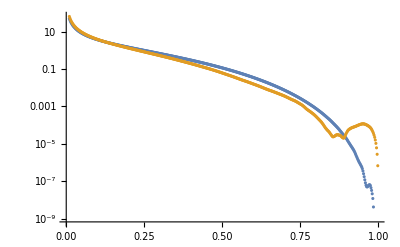

```mathematica
ListLogPlot[{f1dDataWW,f1dDataNN}]
```

```mathematica
f1d=Interpolation[f1dDataWW]
```

InterpolatingFunction[…]

```mathematica
f1u=Interpolation[f1uDataWW]
```

InterpolatingFunction[…]

```mathematica
g1d=Interpolation[g1dDataWW]
```

InterpolatingFunction[…]

```mathematica
g1u=Interpolation[g1uDataWW]
```

InterpolatingFunction[…]

```mathematica
f1dTMDpart[kT_]:=1/(0.25π)Exp[-kT^2/0.25]
```

```mathematica
f1uTMDpart[kT_]:=1/(0.25π)Exp[-kT^2/0.25]
```

## Constants & global functions

Units of GeV

```mathematica
M=3.1;
m=M/2;
Λ=0.2;
nf=5;
Nc=3;
(* Chao et al. values for LDMEs *)
OJψ3S1sing=1.16;
OJψ3S1oct=0.3 10^-2;
OJψ1S0oct=8.9 10^-2;
OJψ3P0oct=m^2 0.56 10^-2;
s=63.0^2;
αem=1.0/137;
gem=√(4π αem);
avP=0.25;
avz=0.04;
αs[μ_]:=(2π)/((11-(2nf)/3)Log[μ/Λ])
gs[μ_]:=√(4π αs[μ])
```

```mathematica
(* bins: {{xmin,xmax},{zmin,zmax},{Qmin,Qmax},{Pperpmin,Pperpmax}} *)
bin[1]={{0.1,0.5},{0.1,0.4},{10.0,30.0},{0.01,0.51},2 10^3};
bin[2]={{0.1,0.5},{0.1,0.4},{30.0,50.0},{0.01,1.51},2 10^6};
bin[3]={{0.1,0.5},{0.4,0.8},{10.0,30.0},{0.01,2.01},2 10^3};
bin[4]={{0.1,0.5},{0.4,0.8},{30.0,50.0},{0.01,6.01},5 10^6};
bin[5]={{0.5,1.0},{0.1,0.4},{10.0,30.0},{0.01,0.51},2 10^5};
bin[6]={{0.5,1.0},{0.1,0.4},{30.0,50.0},{0.01,1.51},5 10^6};
bin[7]={{0.5,1.0},{0.4,0.8},{10.0,30.0},{0.01,2.01},2 10^5};
bin[8]={{0.5,1.0},{0.4,0.8},{30.0,50.0},{0.01,6.01},2 10^7};
```

```mathematica
(* 2Q factor to go from d/dQ^2, constant to go to pb units *)
```

```mathematica
dσPlot[crosssections_,{{xmin_,xmax_},{zmin_,zmax_},{Qmin_,Qmax_},{Pperpmin_,Pperpmax_},norm_}]:=
Module[{func,colors,labels,toPlot},
Do[
func[i]=Interpolation[Table[{Pperp,
NIntegrate[2Q norm crosssections[[i]][x,z,Q,Pperp],{x,xmin,xmax},{z,zmin,zmax},{Q,Qmin,Qmax},Method->{"LocalAdaptive","SingularityHandler"->"IMT"}]}
,{Pperp,Pperpmin,Pperpmax,(Pperpmax-Pperpmin)/10}]]
,{i,1,Length[crosssections]}];
colors={Red,Blue,Green,Purple,Orange,Black};
labels=Table[ToString[crosssections[[i]]],{i,1,Length[crosssections]}];
toPlot=Table[func[i][PT],{i,1,Length[crosssections]}];
Plot[toPlot,{PT,Pperpmin,Pperpmax},PlotRange->{0,All},AspectRatio->1,PlotStyle->Table[colors[[i]],{i,1,Length[toPlot]}],PlotLegends->labels,BaseStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameStyle->Black,PlotLabel->"x∈["<>ToString[xmin]<>","<>ToString[xmax]<>"],z∈["<>ToString[zmin]<>","<>ToString[zmax]<>"],Q∈["<>ToString[Qmin]<>","<>ToString[Qmax]<>"]",FrameLabel->{"P_⊥ [GeV]",ToString[norm]<>"*dσ/(dP_⊥)^2"},ImageSize->300]
]//Quiet
```

## Photon-gluon fusion cross sections

## Cross sections

dσ/(dx dz dQ^2 dPperp^2).

### 1s0 octet

```mathematica
dσ1S0octU[x_,z_,Q_,Pperp_]:=Piecewise[{{1/(2.568 10^-9)3(*factor of 3 from summing over all polarizations (think: sum over SLL = 1/2,1/2,-1 but the expression is independent of SLL)*)((16 ⅇ^(-Pperp^2/avP-(-1+z)^2/avz) OJψ1S0oct π^(3/2) ((M^2+Pperp^2)^2 (Q^4-2 Q^2 s x+2 s^2 x^2)-2 Q^2 (4 Pperp^2 s x (Q^2-s x)-M^2 (Q^4-2 Q^2 s x+2 s^2 x^2)) z^2+Q^4 (Q^4-2 Q^2 s x+2 s^2 x^2) z^4) αem^2 gPDF[(x (M^2+Pperp^2-Q^2 (-2+z) z))/(Q^2 z)] αs[30])/(27 avP √avz M Q^4 s^2 x^2 (M^2+Pperp^2-Q^2 (-2+z) z)^3)),x(Q^2+M^2)/Q^2<=(x (M^2+Pperp^2-Q^2 (-2+z) z))/(Q^2 z)<=1&&0<=Q^2/(x s)<=1}}]
```

```mathematica
dσ1S0octL[x_,z_,Q_,Pperp_]:=1/3 dσ1S0octU[x,z,Q,Pperp]
```

### 3p0 octet

```mathematica
dσ3P0octU[x_,z_,Q_,Pperp_]:=Piecewise[{{1/(2.568 10^-9)((64 ⅇ^(-Pperp^2/avP-(-1+z)^2/avz) OJψ3P0oct π^(3/2) (2 Pperp^10 s x (-Q^2+s x)+2 M^10 s x (Q^2-s x) (-1+z)+Pperp^8 Q^2 z (2 Q^2 s x (-4+z)-2 s^2 x^2 (-4+z)+Q^4 (3+2 z))-2 Pperp^2 Q^8 z^5 (Q^2 s x (16-8 z+z^3)-s^2 x^2 (16-8 z+z^3)+Q^4 z (-4+z (2+z)))+Q^10 z^7 (2 Q^2 s x (-2+z) (4+(-2+z) z)-2 s^2 x^2 (-2+z) (4+(-2+z) z)+Q^4 (8+z (-8+3 z)))-2 Pperp^6 Q^4 z^2 (-2 Q^2 s x (-4+z^2)+2 s^2 x^2 (-4+z^2)+Q^4 (-4+z (2+3 z)))+2 Pperp^4 Q^6 z^3 (-2 Q^2 s x (4+(-2+z)^2 z)+2 s^2 x^2 (4+(-2+z)^2 z)+Q^4 (4+z (-4+z+3 z^2)))+M^8 (2 Pperp^2 s x (Q^2-s x) (-5+4 z)+Q^2 z (Q^4 (3-4 z+8 z^2)-2 Q^2 s x (4+z (-5+8 z))+2 s^2 x^2 (4+z (-5+8 z))))+2 M^2 (Pperp^8 s x (Q^2-s x) (-5+z)+Pperp^6 Q^2 z (8 Q^2 s x (-2+z)-8 s^2 x^2 (-2+z)+Q^4 (6+z-z^2))+Q^8 z^5 (2 Q^4 (-3+z) (4+(-6+z) z)+s^2 x^2 (16-(-1+z) z (-8+(-4+z) z))+Q^2 s x (-16+(-1+z) z (-8+(-4+z) z)))+2 Pperp^4 Q^4 z^2 (-Q^2 s x (-3+z) (-4+(-2+z) z)+s^2 x^2 (-3+z) (-4+(-2+z) z)+Q^4 (6+z (-11+(-2+z) z)))+Pperp^2 Q^6 z^3 (-8 Q^2 s x (2+z (2+(-1+z) z))+8 s^2 x^2 (2+z (2+(-1+z) z))+Q^4 (8-(-6+z) z (-8+z (5+z)))))+2 M^6 (2 Pperp^4 s x (Q^2-s x) (-5+3 z)+Pperp^2 Q^2 z (-16 Q^2 s x (1+(-1+z) z)+16 s^2 x^2 (1+(-1+z) z)+Q^4 (6+z (-5+7 z)))-2 Q^4 z^2 (Q^2 s x (4+z (2-3 z+9 z^2))-s^2 x^2 (4+z (2-3 z+9 z^2))+Q^4 (-2+z (9+z (-19+8 z)))))+2 M^4 (2 Pperp^6 s x (Q^2-s x) (-5+2 z)+Pperp^4 Q^2 z (Q^4 (9+z (-3+2 z))-2 Q^2 s x (12+z (-9+4 z))+2 s^2 x^2 (12+z (-9+4 z)))+Q^6 z^3 (-2 Q^2 s x (4+4 z+3 z^3+4 z^4)+2 s^2 x^2 (4+4 z+3 z^3+4 z^4)+Q^4 (-2+z) (-2+z (21-30 z+4 z^2)))+Pperp^2 Q^4 z^2 (Q^4 (12+z (-38+z (37+2 z)))-2 Q^2 s x (12+z (4+z (-7+10 z)))+2 s^2 x^2 (12+z (4+z (-7+10 z)))))) αem^2 gPDF[(x (M^2+Pperp^2-Q^2 (-2+z) z))/(Q^2 z)] αs[30])/(9 avP √avz M^3 Q^6 s^2 x^2 z (M^2+Pperp^2-Q^2 (-2+z) z)^5)),x(Q^2+M^2)/Q^2<=(x (M^2+Pperp^2-Q^2 (-2+z) z))/(Q^2 z)<=1&&0<=Q^2/(x s)<=1}}]
```

```mathematica
dσ3P0octL[x_,z_,Q_,Pperp_]:=Piecewise[{{1/(2.568 10^-9)((64 ⅇ^(-Pperp^2/avP-(-1+z)^2/avz) OJψ3P0oct π^(3/2) (2 M^14 s x (Q^2-s x) (-1+z)-(Pperp^4-Q^4 z^4)^2 (2 Pperp^6 s x (Q^2-s x)-Q^6 z^5 ((Q^2-2 s x)^2+2 s x (Q^2-s x) z)-Pperp^4 Q^2 z ((Q^2-2 s x)^2+2 (Q^4-3 Q^2 s x+3 s^2 x^2) z)+2 Pperp^2 Q^4 z^3 (Q^2 s x (8-3 z)+Q^4 (-1+z)+s^2 x^2 (-8+3 z)))+M^12 (2 Pperp^2 s x (Q^2-s x) (-7+6 z)+Q^2 z (-1+2 z) (2 Q^2 s x (2-3 z)+Q^4 (-1+2 z)+2 s^2 x^2 (-2+3 z)))+2 M^10 (3 Pperp^4 s x (Q^2-s x) (-7+5 z)+Q^4 z^3 (Q^4 (-9+2 (9-4 z) z)-Q^2 s x (-12+z (21+z))+s^2 x^2 (-12+z (21+z)))+Pperp^2 Q^2 z (-4 Q^2 s x (-1+z) (-3+5 z)+4 s^2 x^2 (-1+z) (-3+5 z)+Q^4 (3+z (-9+7 z))))+M^8 (10 Pperp^6 s x (Q^2-s x) (-7+4 z)+Pperp^4 Q^2 z (-10 Q^2 s x (-2+z) (-3+4 z)+10 s^2 x^2 (-2+z) (-3+4 z)+Q^4 (15+2 z (-15+8 z)))-2 Pperp^2 Q^4 z^3 (s^2 x^2 (40-z (63+4 z))+Q^2 s x (-40+z (63+4 z))+Q^4 (35+z (-55+16 z)))+Q^6 z^4 (2 Q^2 s x z (-46+z (35+12 z))-2 s^2 x^2 z (-46+z (35+12 z))+Q^4 (-32+z (95+8 z (-11+3 z)))))+2 M^6 (5 Pperp^8 s x (Q^2-s x) (-7+3 z)+2 Pperp^6 Q^2 z (5 (Q^2-2 s x)^2-5 (Q^2-2 s x)^2 z+Q^4 z^2)-2 Pperp^4 Q^4 z^3 (Q^4 (25+4 (-7+z) z)+s^2 x^2 (20-z (29+3 z))+Q^2 s x (-20+z (29+3 z)))+Q^8 z^5 (-Q^2 s x (16+z^2 (-72+z (35+z)))+s^2 x^2 (16+z^2 (-72+z (35+z)))-2 Q^4 (-2+z) (-2+z (11+2 z (-7+2 z))))-2 Pperp^2 Q^6 z^4 (4 Q^2 s x z (13+2 (-6+z) z)-4 s^2 x^2 z (13+2 (-6+z) z)+Q^4 (24+z (-51+z (19+3 z)))))+M^4 (6 Pperp^10 s x (Q^2-s x) (-7+2 z)+4 Pperp^6 Q^4 z^3 (-Q^2 s x z (3+2 z)+s^2 x^2 z (3+2 z)+3 Q^4 (-5+3 z))+Pperp^8 Q^2 z (Q^4 (15-4 z^2)+10 Q^2 s x (-6+z+2 z^2)-10 s^2 x^2 (-6+z+2 z^2))+2 Pperp^4 Q^6 z^4 (-2 Q^2 s x z (34+z (-31+2 z))+2 s^2 x^2 z (34+z (-31+2 z))+Q^4 (-48+z (61+6 z)))-2 Pperp^2 Q^8 z^5 (s^2 x^2 (-32+z (32-z (32+z) (-3+2 z)))+Q^2 s x (32+z (-32+z (32+z) (-3+2 z)))+2 Q^4 (8+z (-24+z (7+3 z))))+Q^10 z^7 (2 Q^2 s x (32+z^2 (-46+3 (7-2 z) z))+2 s^2 x^2 (-32+z^2 (46+3 z (-7+2 z)))+Q^4 (32+z (-96+z (95+4 (-9+z) z)))))+2 M^2 (Pperp^12 s x (Q^2-s x) (-7+z)-Pperp^8 Q^4 z^3 (Q^4 (5+2 z)+Q^2 s x (20+(-15+z) z)-s^2 x^2 (20+(-15+z) z))+Pperp^10 Q^2 z (4 Q^2 s x (-3+z) (1+z)-4 s^2 x^2 (-3+z) (1+z)+Q^4 (3-(-3+z) z))-Pperp^2 Q^10 z^8 (Q^4 z (-7+z+z^2)-4 Q^2 s x (-8-3 z+z^3)+4 s^2 x^2 (-8-3 z+z^3))+2 Pperp^6 Q^6 z^4 (-4 Q^2 s x z (1+(-1+z) z)+4 s^2 x^2 z (1+(-1+z) z)+Q^4 (-8+z (3+(-1+z) z)))+Q^12 z^9 (Q^2 s x (-16+(-4+z) (-3+z) z^2)-s^2 x^2 (-16+(-4+z) (-3+z) z^2)+Q^4 (-8+z (16+z (-9+2 z))))+Pperp^4 Q^8 z^5 (2 Q^4 (-4+7 z^2)-Q^2 s x (16+z (-32+z (56+z+z^2)))+s^2 x^2 (16+z (-32+z (56+z+z^2)))))) αem^2 gPDF[(x (M^2+Pperp^2-Q^2 (-2+z) z))/(Q^2 z)] αs[30])/(9 avP √avz M^3 Q^6 s^2 x^2 z (M^2+Pperp^2-Q^2 (-2+z) z)^5 (M^4+2 M^2 (Pperp-Q z) (Pperp+Q z)+(Pperp^2+Q^2 z^2)^2))),x(Q^2+M^2)/Q^2<=(x (M^2+Pperp^2-Q^2 (-2+z) z))/(Q^2 z)<=1&&0<=Q^2/(x s)<=1}}]
```

### 3s1 sing

```mathematica
dσ3S1singU[x_,z_,Q_,Pperp_]:=Piecewise[{{1/(2.568 10^-9)(-((256 OJψ3S1sing π (M^6 (Q^4-2 Q^2 s x+2 s^2 x^2) (-1+z)^4+Pperp^2 Q^2 (2 Pperp^2 s x (-Q^2+s x)+Q^2 (Q^4-2 Q^2 s x+2 s^2 x^2) (-1+z)^2) z^2+M^4 (-1+z)^2 (-Q^2 (4 Q^2 s x-4 s^2 x^2+Q^4 (-2+z)) (-1+z)^2 z+Pperp^2 (Q^4-2 Q^2 s x+2 s^2 x^2) (2+(-2+z) z))+M^2 (Q^4 (Q^4-2 Q^2 s x+2 s^2 x^2) (-1+z)^4 z^2 (2+(-2+z) z)+Pperp^4 (Q^4-2 Q^2 s x+2 s^2 x^2) (1+(-1+z) z)^2+2 Pperp^2 Q^2 (-1+z)^2 z (Q^4-2 Q^2 s x (1+2 (-1+z)^2 z)+2 s^2 x^2 (1+2 (-1+z)^2 z)))) αem^2 gPDF[x+(x (-Pperp^2+M^2 (-1+z)))/(Q^2 (-1+z) z)] αs[30]^2)/(243 M Q^4 s^2 x^2 (Pperp^2+M^2 (-1+z)^2)^2 (M^2+Pperp^2-Q^2 (-2+z) z)^2 (-Pperp^2+(-1+z) (M^2+Q^2 z))))),x(Q^2+M^2)/Q^2<=x+(x (-Pperp^2+M^2 (-1+z)))/(Q^2 (-1+z) z)<=1&&0<=Q^2/(x s)<=1}}]
```

```mathematica
dσ3S1singL[x_,z_,Q_,Pperp_]:=Piecewise[{{1/(2.568 10^-9)(-((256 OJψ3S1sing π z^2 (M^8 (Pperp^2 (Q^4-2 Q^2 s x+2 s^2 x^2)-2 Q^2 s x (Q^2-s x) (-1+z)^2) (-1+z)^2-Pperp^2 Q^2 (2 Pperp^2 s x (Q^2-s x)-Q^2 (Q^4-2 Q^2 s x+2 s^2 x^2) (-1+z)^2) (Pperp^2+Q^2 z^2)^2+2 M^6 (1-z) (Pperp^4 (Q^4-2 Q^2 s x+2 s^2 x^2)+Pperp^2 Q^6 (-1+z)^3-2 Q^4 s x (Q^2-s x) (-1+z)^3 z^2)+2 M^2 Pperp^2 Q^2 (Pperp^2+Q^2 z^2) (Q^2 (Q^4-2 Q^2 s x+2 s^2 x^2) (-1+z)^4+Pperp^2 (Q^4 (-1+z)+2 Q^2 s x (3-2 z) z+2 s^2 x^2 z (-3+2 z)))-M^4 (2 Q^6 s x (Q^2-s x) (-1+z)^4 z^4-Pperp^6 (Q^4-2 Q^2 s x+2 s^2 x^2) (1+z^2)-Pperp^2 Q^4 (-1+z)^2 (-2 Q^2 s x (1+z (-4+(-2+z)^2 z))+2 s^2 x^2 (1+z (-4+(-2+z)^2 z))+Q^4 (1+(-2+z) z (2+z (-2+3 z))))-2 Pperp^4 Q^2 (Q^4 (-2+z) (-1+z)^2+Q^2 s x (2+z (2+z (-18+(18-5 z) z)))+s^2 x^2 (-2+z (-2+z (18+z (-18+5 z))))))) αem^2 gPDF[x+(x (-Pperp^2+M^2 (-1+z)))/(Q^2 (-1+z) z)] αs[30]^2)/(243 M Q^4 s^2 x^2 (Pperp^2+M^2 (-1+z)^2)^2 (M^2+Pperp^2-Q^2 (-2+z) z)^2 (Pperp^2+(M-Q z)^2) (Pperp^2+(M+Q z)^2) (-Pperp^2+(-1+z) (M^2+Q^2 z))))),x(Q^2+M^2)/Q^2<=x+(x (-Pperp^2+M^2 (-1+z)))/(Q^2 (-1+z) z)<=1&&0<=Q^2/(x s)<=1}}]
```

### 1s0 octet (2ϕ)

```mathematica
dσ1S0octU2ϕ[x_,z_,Q_,Pperp_]:=Piecewise[{{1/(2.568 10^-9)3(*factor of 3 from summing over all polarizations (think: sum over SLL = 1/2,1/2,-1 but the expression is independent of SLL)*)(-(32 ⅇ^(-Pperp^2/avP-(-1+z)^2/avz) OJψ1S0oct √π Pperp^2 (-1+Q^2/(s x)) z^2 αem^2 gPDF[(x (M^2+Pperp^2-Q^2 (-2+z) z))/(Q^2 z)] αs[30])/(27 avP √avz M Q^2 (M^2+Pperp^2-Q^2 (-2+z) z)^3)),x(Q^2+M^2)/Q^2<=(x (M^2+Pperp^2-Q^2 (-2+z) z))/(Q^2 z)<=1&&0<=Q^2/(x s)<=1}}]
```

```mathematica
dσ1S0octL2ϕ[x_,z_,Q_,Pperp_]:=1/3 dσ1S0octU[x,z,Q,Pperp]
```

### 3p0 octet (2ϕ)

These cross sections have NOT yet been integrated over ϕ.

```mathematica
dσ3P0octU2ϕ[x_,z_,Q_,Pperp_]:=Piecewise[{{1/(2.568 10^-9)(-((128 ⅇ^(-Pperp^2/avP-(-1+z)^2/avz) OJψ3P0oct √π Pperp^2 (-1+Q^2/(s x)) z (-M^6 (-1+z)+(Pperp^2-Q^2 (-2+z) z) (Pperp^4-2 Pperp^2 Q^2 (-1+z) z+Q^4 z^2 (4+(-2+z) z))+M^4 (Pperp^2 (3-2 z)+Q^2 z (4+z (-7+10 z)))+M^2 (-Pperp^4 (-3+z)+2 Pperp^2 Q^2 (-4+z) (-1+z) z-Q^4 z^2 (-8+z (4+(-7+z) z)))) αem^2 gPDF[(x (M^2+Pperp^2-Q^2 (-2+z) z))/(Q^2 z)] αs[30])/(9 avP √avz M^3 Q^4 (M^2+Pperp^2-Q^2 (-2+z) z)^5))),x(Q^2+M^2)/Q^2<=(x (M^2+Pperp^2-Q^2 (-2+z) z))/(Q^2 z)<=1&&0<=Q^2/(x s)<=1}}]
```

```mathematica
dσ3P0octL2ϕ[x_,z_,Q_,Pperp_]:=Piecewise[{{1/(2.568 10^-9)(-((128 ⅇ^(-Pperp^2/avP-(-1+z)^2/avz) OJψ3P0oct √π Pperp^2 (-1+Q^2/(s x)) z ((M^2+Pperp^2)^5-(M^2+Pperp^2)^4 (M^2-2 Q^2) z-(M^2+Pperp^2)^4 Q^2 z^2+2 (M^2+Pperp^2) Q^4 (7 M^4-Pperp^4-2 M^2 (Pperp^2+4 Q^2)) z^4+2 Q^4 (-7 M^6-2 Pperp^4 Q^2+2 M^4 (Pperp^2+7 Q^2)+M^2 (Pperp^4+4 Pperp^2 Q^2-8 Q^4)) z^5+2 Q^6 (-7 M^4+Pperp^4+2 M^2 (Pperp^2+4 Q^2)) z^6+(M^2+Pperp^2) Q^8 z^8+Q^8 (-M^2+2 Q^2) z^9-Q^10 z^10) αem^2 gPDF[(x (M^2+Pperp^2-Q^2 (-2+z) z))/(Q^2 z)] αs[30])/(9 avP √avz M^3 Q^4 (M^2+Pperp^2-Q^2 (-2+z) z)^5 (Pperp^2+(M-Q z)^2) (Pperp^2+(M+Q z)^2)))),x(Q^2+M^2)/Q^2<=(x (M^2+Pperp^2-Q^2 (-2+z) z))/(Q^2 z)<=1&&0<=Q^2/(x s)<=1}}]
```

### 3s1 sing (2ϕ)

These cross sections have NOT yet been integrated over ϕ.

```mathematica
dσ3S1singU2ϕ[x_,z_,Q_,Pperp_]:=Piecewise[{{1/(2.568 10^-9)(-(256 M OJψ3S1sing Pperp^2 (Q^2-s x) (-1+z)^2 z^2 (M^2+Q^2 (-1-2 (-2+z) z)) αem^2 gPDF[x+(x (-Pperp^2+M^2 (-1+z)))/(Q^2 (-1+z) z)] αs[30]^2)/(243 Q^4 s x (Pperp^2+M^2 (-1+z)^2)^2 (M^2+Pperp^2-Q^2 (-2+z) z)^2 (-Pperp^2+(-1+z) (M^2+Q^2 z)))),x(Q^2+M^2)/Q^2<=x+(x (-Pperp^2+M^2 (-1+z)))/(Q^2 (-1+z) z)<=1&&0<=Q^2/(x s)<=1}}]
```

```mathematica
dσ3S1singL2ϕ[x_,z_,Q_,Pperp_]:=Piecewise[{{1/(2.568 10^-9)(-((512 M OJψ3S1sing Pperp^2 (Q^2-s x) z^3 (M^4 Pperp^2 (-1+z)-M^2 (Pperp+Q (-1+z)) (Pperp+Q-Q z) (Pperp^2+Q^2 (-1+z)^2 z)-Pperp^2 Q^2 (-1+z) (Pperp^2+Q^2 z^2)) αem^2 gPDF[x+(x (-Pperp^2+M^2 (-1+z)))/(Q^2 (-1+z) z)] αs[30]^2)/(243 Q^4 s x (Pperp^2+M^2 (-1+z)^2)^2 (M^2+Pperp^2-Q^2 (-2+z) z)^2 (Pperp^2+(M-Q z)^2) (Pperp^2+(M+Q z)^2) (-Pperp^2+(-1+z) (M^2+Q^2 z))))),x(Q^2+M^2)/Q^2<=x+(x (-Pperp^2+M^2 (-1+z)))/(Q^2 (-1+z) z)<=1&&0<=Q^2/(x s)<=1}}]
```

### Total PGF cross sections

```mathematica
dσPGFColorOctetU[x_,z_,Q_,Pperp_]:=dσ1S0octU[x,z,Q,Pperp]+dσ3P0octU[x,z,Q,Pperp]
dσPGFColorOctetL[x_,z_,Q_,Pperp_]:=dσ1S0octL[x,z,Q,Pperp]+dσ3P0octL[x,z,Q,Pperp]
dσPGFU[x_,z_,Q_,Pperp_]:=dσPGFColorOctetU[x,z,Q,Pperp]+dσ3S1singU[x,z,Q,Pperp]
dσPGFL[x_,z_,Q_,Pperp_]:=dσPGFColorOctetL[x,z,Q,Pperp]+dσ3S1singL[x,z,Q,Pperp]
```

```mathematica
dσPGFU2ϕ[x_,z_,Q_,Pperp_]:=dσ1S0octU2ϕ[x,z,Q,Pperp]+dσ3P0octU2ϕ[x,z,Q,Pperp]+dσ3S1singU2ϕ[x,z,Q,Pperp]
dσPGFL2ϕ[x_,z_,Q_,Pperp_]:=dσ1S0octL2ϕ[x,z,Q,Pperp]+dσ3P0octL2ϕ[x,z,Q,Pperp]+dσ3S1singL2ϕ[x,z,Q,Pperp]
```

## Color octet ^3 S_1^[8] quark fragmentation

## Cross sections & FFs

### FFs

```mathematica
D1=Compile[{{z,_Real},{kT,_Real}},(2 αs[M]^2 OJψ3S1oct)/(27 π M^3 z(M^2(z-1)-kT^2 z^2)^2)(kT^2 z^2((z-2)z+2)+2 M^2(z-1)^2)]
```

CompiledFunction[…]

```mathematica
D1LL=Compile[{{z,_Real},{kT,_Real}},(2 αs[M]^2 OJψ3S1oct)/(27 π M^3 z(M^2(z-1)-kT^2 z^2)^2)(kT^2 z^2((z-2)z+2)-4 M^2(z-1)^2)]
```

CompiledFunction[…]

### Cross sections

If we use the expression for the cross sections in 0007120 but without the factor of 2z in the I[] convolution integral, then our matches Yiannis Eq 4.3.  Do that here.

dσ/(dx dz dQ^2 dPperp^2).

```mathematica
dσFragU[x_,z_,Q_,Pperp_]:=
Piecewise[{{1/(2.568 10^-9)3(*3 from sum over polarizations*)(2 π^2 (Q^4-2 Q^2 s x+2 s^2 x^2) αem^2)/(Q^4 s^2 x^2)((2/3)^2 f1u[x]+(1/3)^2 f1d[x])D1[z,Pperp/z],0<=Q^2/(x s)<=1}}]//Quiet
dσFragL[x_,z_,Q_,Pperp_]:=Piecewise[{{1/(2.568 10^-9)(2 π^2 (Q^4-2 Q^2 s x+2 s^2 x^2) αem^2)/(Q^4 s^2 x^2)((2/3)^2 f1u[x]+(1/3)^2 f1d[x])(D1[z,Pperp/z]-D1LL[z,Pperp/z]),0<=Q^2/(x s)<=1}}]//Quiet
dσFragT[x_,z_,Q_,Pperp_]:=dσFragU[x,z,Q,Pperp]-dσFragL[x,z,Q,Pperp]
```

```mathematica
dσLLFragU[x_,z_,Q_,Pperp_]:=
Piecewise[{{1/(2.568 10^-9)3(*3 from sum over polarizations*)(-2 π^2 SqL (Q^2-2 s x) αem^2 λe)/(Q^2 s^2 x^2)((2/3)^2 g1u[x]+(1/3)^2 g1d[x])D1[z,Pperp/z],0<=Q^2/(x s)<=1}}]//Quiet
dσLLFragL[x_,z_,Q_,Pperp_]:=Piecewise[{{1/(2.568 10^-9)(-2 π^2 SqL (Q^2-2 s x) αem^2 λe)/(Q^2 s^2 x^2)((2/3)^2 g1u[x]+(1/3)^2 g1d[x])(D1[z,Pperp/z]-D1LL[z,Pperp/z]),0<=Q^2/(x s)<=1}}]//Quiet
dσLLFragT[x_,z_,Q_,Pperp_]:=dσLLFragU[x,z,Q,Pperp]-dσLLFragL[x,z,Q,Pperp]
```

### Structure functions only

```mathematica
f1D1[x_,z_,Q_,Pperp_]:=Piecewise[{{1/(2.568 10^-9)(2 π^2 (Q^4-2 Q^2 s x+2 s^2 x^2) αem^2)/(Q^4 s^2 x^2)((2/3)^2 f1u[x]+(1/3)^2 f1d[x])(coeffD1 D1[z,Pperp/z]),0<=Q^2/(x s)<=1}}]//Quiet
f1D1LL[x_,z_,Q_,Pperp_]:=Piecewise[{{1/(2.568 10^-9)(2 π^2 (Q^4-2 Q^2 s x+2 s^2 x^2) αem^2)/(Q^4 s^2 x^2)((2/3)^2 f1u[x]+(1/3)^2 f1d[x])(SLL D1LL[z,Pperp/z]),0<=Q^2/(x s)<=1}}]//Quiet
```

## Actual plots for paper

## PGF, FF together

```mathematica
dσFuncs[crosssections_,{{xmin_,xmax_},{zmin_,zmax_},{Qmin_,Qmax_},{Pperpmin_,Pperpmax_},norm_}]:=
Module[{func},
Do[
func[i]=Interpolation[Table[{Pperp,
NIntegrate[2Q crosssections[[i]][x,z,Q,Pperp],{x,xmin,xmax},{z,zmin,zmax},{Q,Qmin,Qmax},Method->{"LocalAdaptive","SingularityHandler"->"IMT"}]}
,{Pperp,Pperpmin,Pperpmax,(Pperpmax-Pperpmin)/32}]]
,{i,1,Length[crosssections]}];
Table[func[i][PT],{i,1,Length[crosssections]}]
]//Quiet
```

```mathematica
(* bins: {{xmin,xmax},{zmin,zmax},{Qmin,Qmax},{Pperpmin,Pperpmax}} *)
bin[1]={{0.1,0.5},{0.1,0.4},{10.0,30.0},{0.01,0.51}, 10^4};
bin[2]={{0.1,0.5},{0.1,0.4},{30.0,50.0},{0.01,1.51},2*10^6};
bin[3]={{0.1,0.5},{0.4,0.8},{10.0,30.0},{0.01,2.01}, 2*10^3};
bin[4]={{0.1,0.5},{0.4,0.8},{30.0,50.0},{0.01,6.01},5* 10^6};
bin[5]={{0.5,1.0},{0.1,0.4},{10.0,30.0},{0.01,0.51},2*10^5};
bin[6]={{0.5,1.0},{0.1,0.4},{30.0,50.0},{0.01,1.51},5*10^6};
bin[7]={{0.5,1.0},{0.4,0.8},{10.0,30.0},{0.01,2.01},5* 10^5};
bin[8]={{0.5,1.0},{0.4,0.8},{30.0,50.0},{0.01,6.01},10^7};
```

```mathematica
DateString[]
funcsU=ParallelTable[dσFuncs[{dσFragU,dσ3S1singU,dσPGFColorOctetU},bin[i]],{i,1,8}];
DateString[]
```

Mon 9 Oct 2023 11:53:09

```mathematica
DateString[]
funcsL=ParallelTable[dσFuncs[{dσFragL,dσ3S1singL,dσPGFColorOctetL},bin[i]],{i,1,8}];
DateString[]
```

Mon 9 Oct 2023 11:53:09

$Aborted

Mon 9 Oct 2023 11:56:23

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

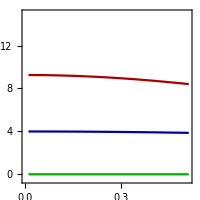
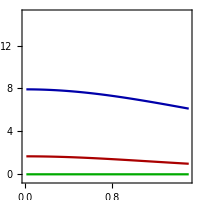
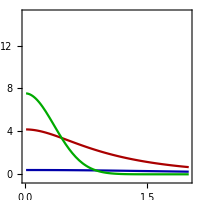
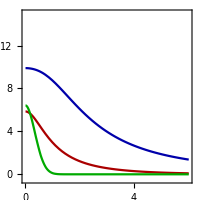
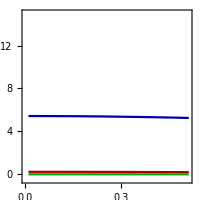
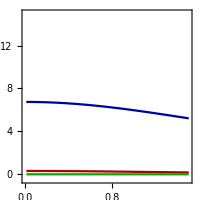
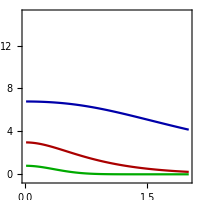
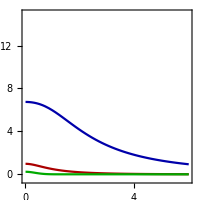
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
normalizedU=Table[bin[i][[5]]funcsU[[i]],{i,1,8}];
SetOptions[MaTeX,Magnification->1.2];
SetOptions[Plot,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameStyle->Black,PlotRange->{-0.5,15},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},ImageSize->200];
normlabels={MaTeX["\\mathcal{N} = 10^4"],MaTeX["\\mathcal{N} = 2 \\times 10^6"],MaTeX["\\mathcal{N} = 2 \\times 10^3"],MaTeX["\\mathcal{N} = 5 \\times 10^6"],MaTeX["\\mathcal{N} = 2 \\times 10^5"],MaTeX["\\mathcal{N} = 5 \\times 10^6"],MaTeX["\\mathcal{N} = 5 \\times 10^5"],MaTeX["\\mathcal{N} = 10^7"]}
padding={{15,3},{15,5}};
PTrange[i_]:={PT,bin[i][[4,1]],bin[i][[4,2]]}
epilog[i_]:=Inset[normlabels[[i]],ImageScaled[{0.95,0.92}],ImageScaled[{1,1}]]
leftonly={Automatic,Directive[FontOpacity->0,FontSize->0]};
noticks=Directive[FontOpacity->0,FontSize->0];
leftandbottom=Automatic;
bottomonly={Directive[FontOpacity->0,FontSize->0],Automatic};
ticksArray[i_]:={leftonly,noticks,noticks,noticks,leftandbottom,bottomonly,bottomonly,bottomonly}[[i]]
Clear[p]
p[i_]:=Plot[Evaluate[normalizedU[[i]]],PTrange[i],FrameTicksStyle->ticksArray[i],Epilog->epilog[i],ImagePadding->padding]
grid=Grid[{{MaTeX["z\\in[0.1,0.4], \\; Q\\in[10,30]\\; {\\rm GeV}"],MaTeX["z\\in[0.1,0.4], \\; Q\\in[30,50]\\; {\\rm GeV}"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[10,30]\\; {\\rm GeV}"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[30,50]\\; {\\rm GeV}"],""},{p[1],p[2],p[3],p[4],Rotate[MaTeX["x\\in[0.1,0.5]"],-90Degree]},{p[5],p[6],p[7],p[8],Rotate[MaTeX["x\\in[0.5,1.0]"],-90Degree]},{"","","",MaTeX["\\; \\; \\; \\;  {\\bf P}_\\perp \\; \\rm [GeV]"],""}},Spacings->{0,0}]
```

```mathematica
legend=LineLegend[{Darker[Blue],Darker[Red],Darker[Green]},{MaTeX["\\gamma^*q \\; (^3S_1^{[8]}) \\;"],MaTeX["\\gamma^*g \\; (^3S_1^{[1]}) \\;"],MaTeX["\\gamma^*g \\; (^1S_0^{[8]}+ \\phantom{}^3P_0^{[8]}) \\;"]},LegendLayout->"Row"]
```

```mathematica
fig=Grid[{{MaTeX["\\mathcal{N}\\frac{d\\sigma}{d{\\bf P}_\\perp^2}\\; {\\rm [pb/GeV^2]},\\; \\sqrt{s}=63 \\; \\rm GeV"]},{legend},{grid}}]
```

-Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
Export["/Users/reedhodges/Desktop/FragAndPGF.pdf",fig]
```

/Users/reedhodges/Desktop/FragAndPGF.pdf

```mathematica
(* bins: {{xmin,xmax},{zmin,zmax},{Qmin,Qmax},{Pperpmin,Pperpmax}} *)
bin[1]={{0.1,0.5},{0.1,0.4},{10.0,30.0},{0.01,0.51}, 2*10^4};
bin[2]={{0.1,0.5},{0.1,0.4},{30.0,50.0},{0.01,1.51},2*10^6};
bin[3]={{0.1,0.5},{0.4,0.8},{10.0,30.0},{0.01,2.01}, 5*10^3};
bin[4]={{0.1,0.5},{0.4,0.8},{30.0,50.0},{0.01,6.01},5* 10^6};
bin[5]={{0.5,1.0},{0.1,0.4},{10.0,30.0},{0.01,0.51},2*10^5};
bin[6]={{0.5,1.0},{0.1,0.4},{30.0,50.0},{0.01,1.51},5*10^6};
bin[7]={{0.5,1.0},{0.4,0.8},{10.0,30.0},{0.01,2.01},5* 10^5};
bin[8]={{0.5,1.0},{0.4,0.8},{30.0,50.0},{0.01,6.01},10^7};
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

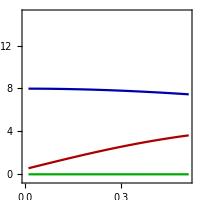
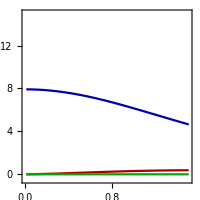
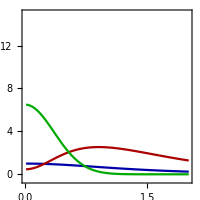
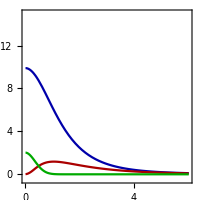
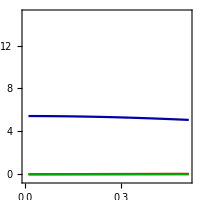
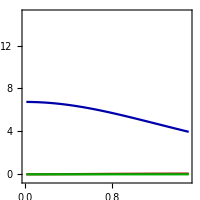
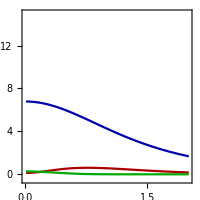
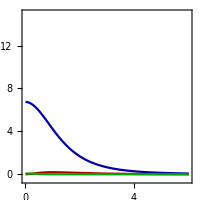
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
normalizedL=Table[bin[i][[5]]funcsL[[i]],{i,1,8}];
SetOptions[MaTeX,Magnification->1.2];
SetOptions[Plot,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameStyle->Black,PlotRange->{-0.5,15},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},ImageSize->200];
normlabels={MaTeX["\\mathcal{N} = 2 \\times 10^4"],MaTeX["\\mathcal{N} = 2 \\times 10^6"],MaTeX["\\mathcal{N} = 5 \\times 10^3"],MaTeX["\\mathcal{N} = 5 \\times 10^6"],MaTeX["\\mathcal{N} = 2 \\times 10^5"],MaTeX["\\mathcal{N} = 5 \\times 10^6"],MaTeX["\\mathcal{N} = 5 \\times 10^5"],MaTeX["\\mathcal{N} = 10^7"]}
padding={{15,3},{15,5}};
PTrange[i_]:={PT,bin[i][[4,1]],bin[i][[4,2]]}
epilog[i_]:=Inset[normlabels[[i]],ImageScaled[{0.95,0.92}],ImageScaled[{1,1}]]
leftonly={Automatic,Directive[FontOpacity->0,FontSize->0]};
noticks=Directive[FontOpacity->0,FontSize->0];
leftandbottom=Automatic;
bottomonly={Directive[FontOpacity->0,FontSize->0],Automatic};
ticksArray[i_]:={leftonly,noticks,noticks,noticks,leftandbottom,bottomonly,bottomonly,bottomonly}[[i]]
Clear[p]
p[i_]:=Plot[Evaluate[normalizedL[[i]]],PTrange[i],FrameTicksStyle->ticksArray[i],Epilog->epilog[i],ImagePadding->padding]
grid=Grid[{{MaTeX["z\\in[0.1,0.4], \\; Q\\in[10,30]\\; {\\rm GeV}"],MaTeX["z\\in[0.1,0.4], \\; Q\\in[30,50]\\; {\\rm GeV}"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[10,30]\\; {\\rm GeV}"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[30,50]\\; {\\rm GeV}"],""},{p[1],p[2],p[3],p[4],Rotate[MaTeX["x\\in[0.1,0.5]"],-90Degree]},{p[5],p[6],p[7],p[8],Rotate[MaTeX["x\\in[0.5,1.0]"],-90Degree]},{"","","",MaTeX["\\; \\; \\; \\;  {\\bf P}_\\perp \\; \\rm [GeV]"],""}},Spacings->{0,0}]
```

```mathematica
fig=Grid[{{MaTeX["\\mathcal{N}\\frac{d\\sigma}{d{\\bf P}_\\perp^2}\\; {\\rm [pb/GeV^2]},\\; \\sqrt{s}=63 \\; \\rm GeV"]},{legend},{grid}}]
```

-Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
Export["/Users/reedhodges/Desktop/FragAndPGFlong.pdf",fig]
```

/Users/reedhodges/Desktop/FragAndPGFlong.pdf

## λ_θ plots

```mathematica
λθ[j_]:=(1-3 Sum[funcsL[[j,i]],{i,1,3}]/Sum[funcsU[[j,i]],{i,1,3}])/(1+Sum[funcsL[[j,i]],{i,1,3}]/Sum[funcsU[[j,i]],{i,1,3}])
```

```mathematica
SetOptions[MaTeX,Magnification->1.2];
SetOptions[Plot,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->12},PlotRange->Automatic,PlotStyle->Darker[Blue],Frame->True,FrameStyle->Black,ImageSize->200];
padding={{45,4},{12,8}};
PTrange[i_]:={PT,bin[i][[4,1]],bin[i][[4,2]]}
leftonly={Automatic,Directive[FontOpacity->0,FontSize->0]};
noticks=Directive[FontOpacity->0,FontSize->0];
leftandbottom=Automatic;
bottomonly={Directive[FontOpacity->0,FontSize->0],Automatic};
ticksArray[i_]:={leftonly,leftonly,leftonly,leftonly,leftandbottom,leftandbottom,leftandbottom,leftandbottom}[[i]]
```

```mathematica
Clear[p]
p[i_]:=Plot[λθ[i],PTrange[i],FrameTicksStyle->ticksArray[i],ImagePadding->padding]
```

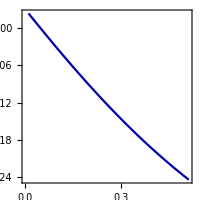
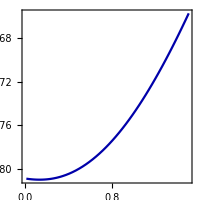
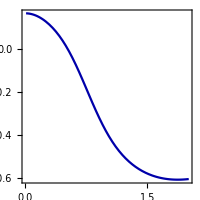
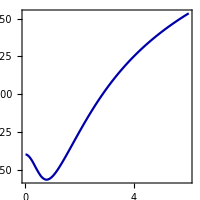
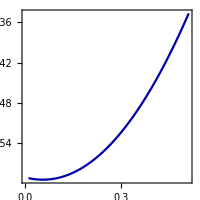
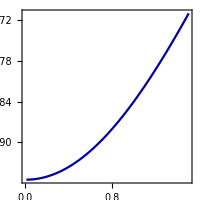
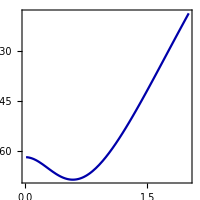
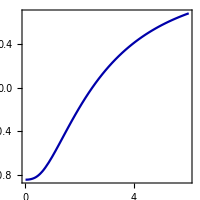
| -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  |  | -Graphics- |

```mathematica
grid=Grid[{{"",MaTeX["\\; \\; \\; \\; z\\in[0.1,0.4], \\; Q\\in[10,30]\\; {\\rm GeV}"],MaTeX["\\; \\; \\; \\; z\\in[0.1,0.4], \\; Q\\in[30,50]\\; {\\rm GeV}"],MaTeX["\\; \\; \\; \\; z\\in[0.4,0.8], \\; Q\\in[10,30]\\; {\\rm GeV}"],MaTeX["\\; \\; \\; \\; z\\in[0.4,0.8], \\; Q\\in[30,50]\\; {\\rm GeV}"],""},{Rotate[MaTeX["\\lambda_\\theta"],90Degree],p[1],p[2],p[3],p[4],Rotate[MaTeX["x\\in[0.1,0.5]"],-90Degree]},{Rotate[MaTeX["\\lambda_\\theta"],90Degree],p[5],p[6],p[7],p[8],Rotate[MaTeX["x\\in[0.5,1.0]"],-90Degree]},{"","","","",MaTeX["\\; \\; \\; \\;  {\\bf P}_\\perp \\; \\rm [GeV]"],""}},Spacings->{0,0}]
```

```mathematica
Export["/Users/reedhodges/Desktop/LambdaTheta.pdf",grid]
```

/Users/reedhodges/Desktop/LambdaTheta.pdf

## FF only -- structure functions

```mathematica
dσFuncs[crosssections_,{{xmin_,xmax_},{zmin_,zmax_},{Qmin_,Qmax_},{Pperpmin_,Pperpmax_},norm_}]:=
Module[{func},
Do[
func[i]=Interpolation[Table[{Pperp,
NIntegrate[2Q crosssections[[i]][x,z,Q,Pperp],{x,xmin,xmax},{z,zmin,zmax},{Q,Qmin,Qmax},Method->{"LocalAdaptive","SingularityHandler"->"IMT"}]}
,{Pperp,Pperpmin,Pperpmax,(Pperpmax-Pperpmin)/32}]]
,{i,1,Length[crosssections]}];
Table[func[i][PT],{i,1,Length[crosssections]}]
]//Quiet
```

```mathematica
(* bins: {{xmin,xmax},{zmin,zmax},{Qmin,Qmax},{Pperpmin,Pperpmax}} *)
bin[1]={{0.1,0.5},{0.1,0.4},{10.0,30.0},{0.01,0.51},10^4};
bin[2]={{0.1,0.5},{0.1,0.4},{30.0,50.0},{0.01,1.51},5*10^5};
bin[3]={{0.1,0.5},{0.4,0.8},{10.0,30.0},{0.01,2.01}, 10^4};
bin[4]={{0.1,0.5},{0.4,0.8},{30.0,50.0},{0.01,6.01},2* 10^6};
bin[5]={{0.5,1.0},{0.1,0.4},{10.0,30.0},{0.01,0.51},10^5};
bin[6]={{0.5,1.0},{0.1,0.4},{30.0,50.0},{0.01,1.51},2*10^6};
bin[7]={{0.5,1.0},{0.4,0.8},{10.0,30.0},{0.01,2.01},2* 10^5};
bin[8]={{0.5,1.0},{0.4,0.8},{30.0,50.0},{0.01,6.01},10^7};
```

```mathematica
DateString[]
coeffD1=2;
SLL=1;
funcs=ParallelTable[dσFuncs[{dσFragT,f1D1,f1D1LL},bin[i]],{i,1,8}];
DateString[]
```

Fri 28 Jul 2023 09:54:34

Fri 28 Jul 2023 09:59:27

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

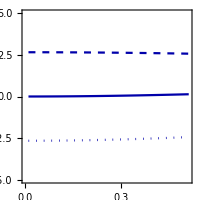
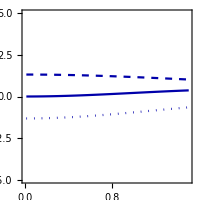
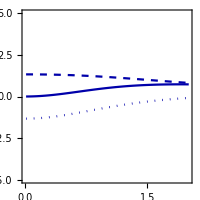
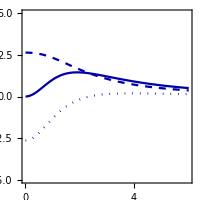
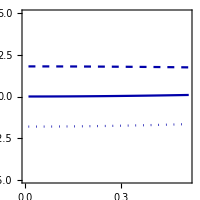
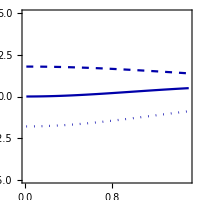
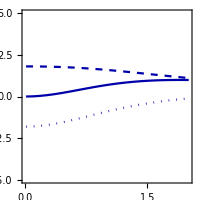
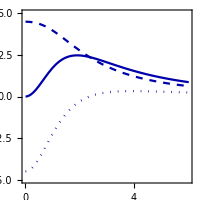
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
normalized=Table[bin[i][[5]]funcs[[i]],{i,1,8}];
SetOptions[MaTeX,Magnification->1.2];
SetOptions[Plot,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameStyle->Black,PlotRange->{-5,5},PlotStyle->{Darker[Blue],{Darker[Blue],Dashed},{Darker[Blue],Dotted}},ImageSize->200];
normlabels={MaTeX["\\mathcal{N} = 10^4"],MaTeX["\\mathcal{N} = 5 \\times 10^5"],MaTeX["\\mathcal{N} = 10^4"],MaTeX["\\mathcal{N} = 2 \\times 10^6"],MaTeX["\\mathcal{N} = 10^5"],MaTeX["\\mathcal{N} = 2 \\times 10^6"],MaTeX["\\mathcal{N} = 2 \\times 10^5"],MaTeX["\\mathcal{N} =  10^7"]}
padding={{15,3},{15,5}};
PTrange[i_]:={PT,bin[i][[4,1]],bin[i][[4,2]]}
epilog[i_]:=Inset[normlabels[[i]],ImageScaled[{0.95,0.92}],ImageScaled[{1,1}]]
leftonly={Automatic,Directive[FontOpacity->0,FontSize->0]};
noticks=Directive[FontOpacity->0,FontSize->0];
leftandbottom=Automatic;
bottomonly={Directive[FontOpacity->0,FontSize->0],Automatic};
ticksArray[i_]:={leftonly,noticks,noticks,noticks,leftandbottom,bottomonly,bottomonly,bottomonly}[[i]]
Clear[p]
p[i_]:=Plot[Evaluate[normalized[[i]]],PTrange[i],FrameTicksStyle->ticksArray[i],Epilog->epilog[i],ImagePadding->padding]
grid=Grid[{{MaTeX["z\\in[0.1,0.4], \\; Q\\in[10,30]"],MaTeX["z\\in[0.1,0.4], \\; Q\\in[30,50]"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[10,30]"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[30,50]"],""},{p[1],p[2],p[3],p[4],Rotate[MaTeX["x\\in[0.1,0.5]"],-90Degree]},{p[5],p[6],p[7],p[8],Rotate[MaTeX["x\\in[0.5,1.0]"],-90Degree]},{"","","",MaTeX["\\; \\; \\; \\;  {\\bf P}_\\perp \\; \\rm [GeV]"],""}},Spacings->{0,0}]
```

```mathematica
legend=LineLegend[{Darker[Blue],{Darker[Blue],Dashed},{Darker[Blue],Dotted}},{MaTeX["d\\sigma_{UU}^T"],MaTeX["2f_1 D_1"],MaTeX["f_1 D_{1LL}"]},LegendLayout->"Row"]
```

```mathematica
fig=Grid[{{MaTeX["\\mathcal{N}\\frac{d\\sigma}{d{\\bf P}_\\perp^2}\\; {\\rm [pb/GeV^2]},\\; \\sqrt{s}=63 \\; \\rm GeV"]},{legend},{grid}}]
```

-Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
DateString[]
coeffD1=1;
SLL=-1;
funcsL=ParallelTable[dσFuncs[{dσFragL,f1D1,f1D1LL},bin[i]],{i,1,8}];
DateString[]
```

Fri 28 Jul 2023 10:08:05

Fri 28 Jul 2023 10:13:04

```mathematica
(* bins: {{xmin,xmax},{zmin,zmax},{Qmin,Qmax},{Pperpmin,Pperpmax}} *)
bin[1]={{0.1,0.5},{0.1,0.4},{10.0,30.0},{0.01,0.51},10^4};
bin[2]={{0.1,0.5},{0.1,0.4},{30.0,50.0},{0.01,1.51},5*10^5};
bin[3]={{0.1,0.5},{0.4,0.8},{10.0,30.0},{0.01,2.01}, 10^4};
bin[4]={{0.1,0.5},{0.4,0.8},{30.0,50.0},{0.01,6.01},2* 10^6};
bin[5]={{0.5,1.0},{0.1,0.4},{10.0,30.0},{0.01,0.51},10^5};
bin[6]={{0.5,1.0},{0.1,0.4},{30.0,50.0},{0.01,1.51},2*10^6};
bin[7]={{0.5,1.0},{0.4,0.8},{10.0,30.0},{0.01,2.01},2* 10^5};
bin[8]={{0.5,1.0},{0.4,0.8},{30.0,50.0},{0.01,6.01},5*10^6};
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

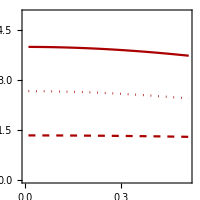
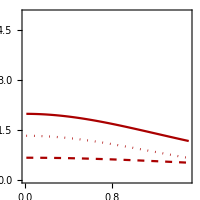
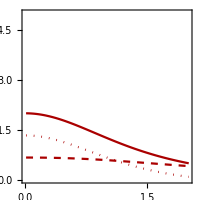
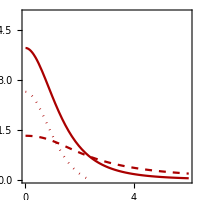
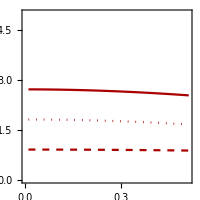
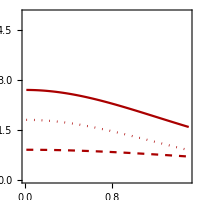
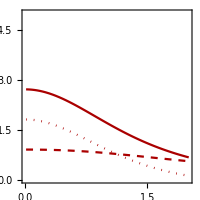
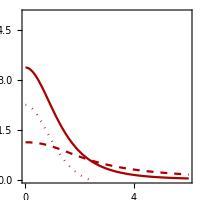
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
normalizedL=Table[bin[i][[5]]funcsL[[i]],{i,1,8}];
SetOptions[MaTeX,Magnification->1.2];
SetOptions[Plot,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameStyle->Black,PlotRange->{0,5},PlotStyle->{Darker[Red],{Darker[Red],Dashed},{Darker[Red],Dotted}},ImageSize->200];
normlabels={MaTeX["\\mathcal{N} = 10^4"],MaTeX["\\mathcal{N} = 5 \\times 10^5"],MaTeX["\\mathcal{N} = 10^4"],MaTeX["\\mathcal{N} = 2 \\times 10^6"],MaTeX["\\mathcal{N} = 10^5"],MaTeX["\\mathcal{N} = 2 \\times 10^6"],MaTeX["\\mathcal{N} = 2 \\times 10^5"],MaTeX["\\mathcal{N} = 5 \\times 10^6"]}
padding={{15,3},{15,5}};
PTrange[i_]:={PT,bin[i][[4,1]],bin[i][[4,2]]}
epilog[i_]:=Inset[normlabels[[i]],ImageScaled[{0.95,0.92}],ImageScaled[{1,1}]]
leftonly={Automatic,Directive[FontOpacity->0,FontSize->0]};
noticks=Directive[FontOpacity->0,FontSize->0];
leftandbottom=Automatic;
bottomonly={Directive[FontOpacity->0,FontSize->0],Automatic};
ticksArray[i_]:={leftonly,noticks,noticks,noticks,leftandbottom,bottomonly,bottomonly,bottomonly}[[i]]
Clear[p]
p[i_]:=Plot[Evaluate[normalizedL[[i]]],PTrange[i],FrameTicksStyle->ticksArray[i],Epilog->epilog[i],ImagePadding->padding]
grid=Grid[{{MaTeX["z\\in[0.1,0.4], \\; Q\\in[10,30]"],MaTeX["z\\in[0.1,0.4], \\; Q\\in[30,50]"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[10,30]"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[30,50]"],""},{p[1],p[2],p[3],p[4],Rotate[MaTeX["x\\in[0.1,0.5]"],-90Degree]},{p[5],p[6],p[7],p[8],Rotate[MaTeX["x\\in[0.5,1.0]"],-90Degree]},{"","","",MaTeX["\\; \\; \\; \\;  {\\bf P}_\\perp \\; \\rm [GeV]"],""}},Spacings->{0,0}]
```

```mathematica
legend=LineLegend[{Darker[Red],{Darker[Red],Dashed},{Darker[Red],Dotted}},{MaTeX["d\\sigma_{UU}^L"],MaTeX["f_1 D_1"],MaTeX["-f_1 D_{1LL}"]},LegendLayout->"Row"]
```

```mathematica
fig=Grid[{{MaTeX["\\mathcal{N}\\frac{d\\sigma}{d{\\bf P}_\\perp^2}\\; {\\rm [pb/GeV^2]},\\; \\sqrt{s}=63 \\; \\rm GeV"]},{legend},{grid}}]
```

-Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
DateString[]
funcsULT=ParallelTable[dσFuncs[{dσFragU,dσFragL,dσFragT},bin[i]],{i,1,8}];
DateString[]
```

Fri 28 Jul 2023 10:14:21

Fri 28 Jul 2023 10:19:32

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

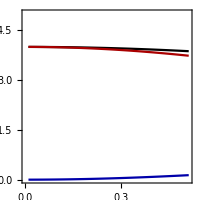
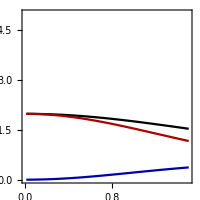
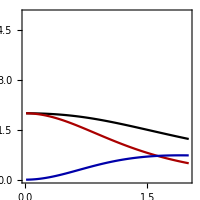
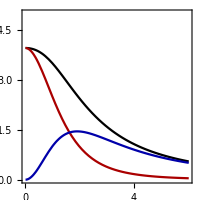
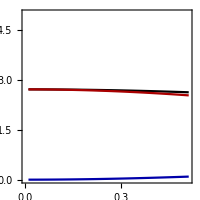
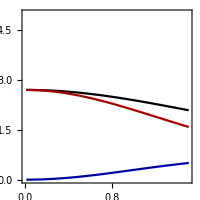
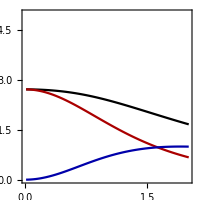
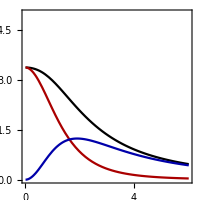
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
normalizedULT=Table[bin[i][[5]]funcsULT[[i]],{i,1,8}];
SetOptions[MaTeX,Magnification->1.2];
SetOptions[Plot,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameStyle->Black,PlotRange->{0,5},PlotStyle->{Black,Darker[Red],Darker[Blue]},ImageSize->200];
normlabels={MaTeX["\\mathcal{N} = 10^4"],MaTeX["\\mathcal{N} = 5 \\times 10^5"],MaTeX["\\mathcal{N} = 10^4"],MaTeX["\\mathcal{N} = 2 \\times 10^6"],MaTeX["\\mathcal{N} = 10^5"],MaTeX["\\mathcal{N} = 2 \\times 10^6"],MaTeX["\\mathcal{N} = 2 \\times 10^5"],MaTeX["\\mathcal{N} = 5 \\times 10^6"]}
padding={{15,3},{15,5}};
PTrange[i_]:={PT,bin[i][[4,1]],bin[i][[4,2]]}
epilog[i_]:=Inset[normlabels[[i]],ImageScaled[{0.95,0.92}],ImageScaled[{1,1}]]
leftonly={Automatic,Directive[FontOpacity->0,FontSize->0]};
noticks=Directive[FontOpacity->0,FontSize->0];
leftandbottom=Automatic;
bottomonly={Directive[FontOpacity->0,FontSize->0],Automatic};
ticksArray[i_]:={leftonly,noticks,noticks,noticks,leftandbottom,bottomonly,bottomonly,bottomonly}[[i]]
Clear[p]
p[i_]:=Plot[Evaluate[normalizedULT[[i]]],PTrange[i],FrameTicksStyle->ticksArray[i],Epilog->epilog[i],ImagePadding->padding]
grid=Grid[{{MaTeX["z\\in[0.1,0.4], \\; Q\\in[10,30]"],MaTeX["z\\in[0.1,0.4], \\; Q\\in[30,50]"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[10,30]"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[30,50]"],""},{p[1],p[2],p[3],p[4],Rotate[MaTeX["x\\in[0.1,0.5]"],-90Degree]},{p[5],p[6],p[7],p[8],Rotate[MaTeX["x\\in[0.5,1.0]"],-90Degree]},{"","","",MaTeX["\\; \\; \\; \\;  {\\bf P}_\\perp \\; \\rm [GeV]"],""}},Spacings->{0,0}]
```

```mathematica
legend=LineLegend[{Black,Darker[Red],Darker[Blue]},{MaTeX["d\\sigma_{UU}^U"],MaTeX["d\\sigma_{UU}^L"],MaTeX["d\\sigma_{UU}^T"]},LegendLayout->"Row"]
```

```mathematica
fig=Grid[{{MaTeX["\\mathcal{N}\\frac{d\\sigma}{d{\\bf P}_\\perp^2}\\; {\\rm [pb/GeV^2]},\\; \\sqrt{s}=63 \\; \\rm GeV"]},{legend},{grid}}]
```

-Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

## dσLL

```mathematica
dσFuncs[crosssections_,{{xmin_,xmax_},{zmin_,zmax_},{Qmin_,Qmax_},{Pperpmin_,Pperpmax_},norm_}]:=
Module[{func},
Do[
func[i]=Interpolation[Table[{Pperp,
NIntegrate[2Q crosssections[[i]][x,z,Q,Pperp],{x,xmin,xmax},{z,zmin,zmax},{Q,Qmin,Qmax},Method->{"LocalAdaptive","SingularityHandler"->"IMT"}]}
,{Pperp,Pperpmin,Pperpmax,(Pperpmax-Pperpmin)/32}]]
,{i,1,Length[crosssections]}];
Table[func[i][PT],{i,1,Length[crosssections]}]
]//Quiet
```

```mathematica
(* bins: {{xmin,xmax},{zmin,zmax},{Qmin,Qmax},{Pperpmin,Pperpmax}} *)
bin[1]={{0.1,0.5},{0.1,0.4},{10.0,30.0},{0.01,0.51},2* 10^5};
bin[2]={{0.1,0.5},{0.1,0.4},{30.0,50.0},{0.01,1.51},2*10^7};
bin[3]={{0.1,0.5},{0.4,0.8},{10.0,30.0},{0.01,2.01},2*10^5};
bin[4]={{0.1,0.5},{0.4,0.8},{30.0,50.0},{0.01,6.01},5*10^7};
bin[5]={{0.5,1.0},{0.1,0.4},{10.0,30.0},{0.01,0.51},5*10^6};
bin[6]={{0.5,1.0},{0.1,0.4},{30.0,50.0},{0.01,1.51},5*10^7};
bin[7]={{0.5,1.0},{0.4,0.8},{10.0,30.0},{0.01,2.01},2*10^7};
bin[8]={{0.5,1.0},{0.4,0.8},{30.0,50.0},{0.01,6.01},2*10^8};
```

```mathematica
DateString[]
SqL=1/2;
λe=1/2;
funcsULT=ParallelTable[dσFuncs[{dσLLFragU,dσLLFragL,dσLLFragT},bin[i]],{i,1,8}];
DateString[]
```

Fri 28 Jul 2023 14:27:36

Fri 28 Jul 2023 14:30:11

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

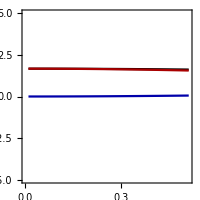
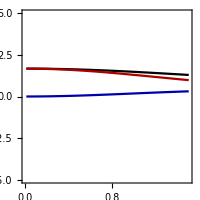
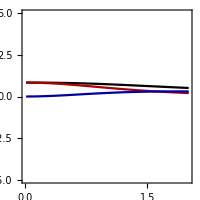
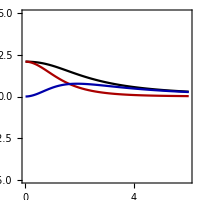
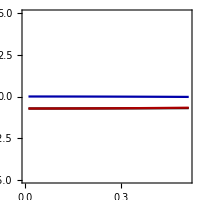
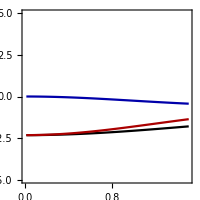
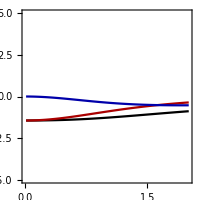
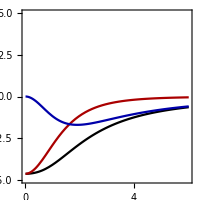
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
normalizedULT=Table[bin[i][[5]]funcsULT[[i]],{i,1,8}];
SetOptions[MaTeX,Magnification->1.2];
SetOptions[Plot,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameStyle->Black,PlotRange->{-5,5},PlotStyle->{Black,Darker[Red],Darker[Blue]},ImageSize->200];
normlabels={MaTeX["\\mathcal{N} = 2 \\times 10^5"],MaTeX["\\mathcal{N} = 2 \\times 10^7"],MaTeX["\\mathcal{N} = 2 \\times 10^5"],MaTeX["\\mathcal{N} = 5 \\times 10^7"],MaTeX["\\mathcal{N} = 5\\times 10^6"],MaTeX["\\mathcal{N} = 5 \\times 10^7"],MaTeX["\\mathcal{N} = 2 \\times 10^6"],MaTeX["\\mathcal{N} = 2 \\times 10^8"]}
padding={{15,3},{15,5}};
PTrange[i_]:={PT,bin[i][[4,1]],bin[i][[4,2]]}
epilog[i_]:=Inset[normlabels[[i]],ImageScaled[{0.95,0.92}],ImageScaled[{1,1}]]
leftonly={Automatic,Directive[FontOpacity->0,FontSize->0]};
noticks=Directive[FontOpacity->0,FontSize->0];
leftandbottom=Automatic;
bottomonly={Directive[FontOpacity->0,FontSize->0],Automatic};
ticksArray[i_]:={leftonly,noticks,noticks,noticks,leftandbottom,bottomonly,bottomonly,bottomonly}[[i]]
Clear[p]
p[i_]:=Plot[Evaluate[normalizedULT[[i]]],PTrange[i],FrameTicksStyle->ticksArray[i],Epilog->epilog[i],ImagePadding->padding]
grid=Grid[{{MaTeX["z\\in[0.1,0.4], \\; Q\\in[10,30]"],MaTeX["z\\in[0.1,0.4], \\; Q\\in[30,50]"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[10,30]"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[30,50]"],""},{p[1],p[2],p[3],p[4],Rotate[MaTeX["x\\in[0.1,0.5]"],-90Degree]},{p[5],p[6],p[7],p[8],Rotate[MaTeX["x\\in[0.5,1.0]"],-90Degree]},{"","","",MaTeX["\\; \\; \\; \\;  {\\bf P}_\\perp \\; \\rm [GeV]"],""}},Spacings->{0,0}]
```

```mathematica
legend=LineLegend[{Black,Darker[Red],Darker[Blue]},{MaTeX["d\\sigma_{LL}^U"],MaTeX["d\\sigma_{LL}^L"],MaTeX["d\\sigma_{LL}^T"]},LegendLayout->"Row"]
```

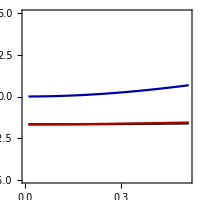
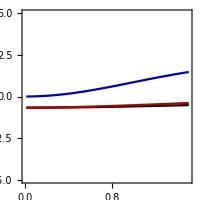
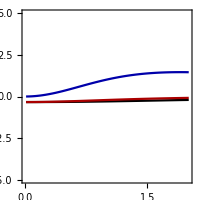
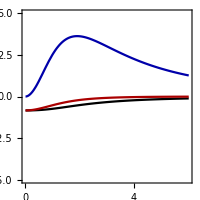
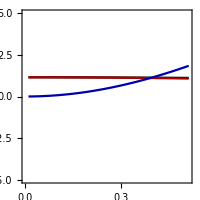
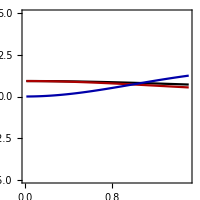
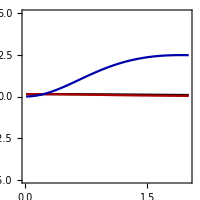
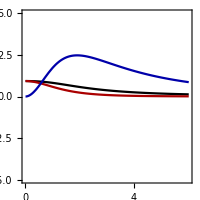
-Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
fig=Grid[{{MaTeX["\\mathcal{N}\\frac{d\\sigma}{d{\\bf P}_\\perp^2}\\; {\\rm [pb/GeV^2]},\\; \\sqrt{s}=63 \\; \\rm GeV"]},{legend},{grid}}]
```

## Cos[2ϕ] asymmetry

The asymmetry is defined as (∫Cos[2ϕ]dσ dϕ)/(∫dσ dϕ).  So in the numerator, only the Cos[2ϕ] contributions to the cross section survive.  Our functions for those contributions have not yet been integrated over ϕ, so our definitions here need to account for that with a factor of π.

```mathematica
dσFuncs[crosssections_,{{xmin_,xmax_},{zmin_,zmax_},{Qmin_,Qmax_},{Pperpmin_,Pperpmax_},norm_}]:=
Module[{func},
Do[
func[i]=Interpolation[Table[{Pperp,
NIntegrate[2Q crosssections[[i]][x,z,Q,Pperp],{x,xmin,xmax},{z,zmin,zmax},{Q,Qmin,Qmax},Method->{"GlobalAdaptive","SingularityHandler"->"IMT"}]}
,{Pperp,Pperpmin,Pperpmax,(Pperpmax-Pperpmin)/8}]]
,{i,1,Length[crosssections]}];
Table[func[i][PT],{i,1,Length[crosssections]}]
]//Quiet
```

```mathematica
(* bins: {{xmin,xmax},{zmin,zmax},{Qmin,Qmax},{Pperpmin,Pperpmax}} *)
bin[1]={{0.1,0.5},{0.1,0.4},{10.0,30.0},{0.01,0.51},1*10^5};
bin[2]={{0.1,0.5},{0.1,0.4},{30.0,50.0},{0.01,1.51},-1*10^5};
bin[3]={{0.1,0.5},{0.4,0.8},{10.0,30.0},{0.01,2.01},5*10^2};
bin[4]={{0.1,0.5},{0.4,0.8},{30.0,50.0},{0.01,6.01},5* 10^3};
bin[5]={{0.5,1.0},{0.1,0.4},{10.0,30.0},{0.01,0.51},5*10^4};
bin[6]={{0.5,1.0},{0.1,0.4},{30.0,50.0},{0.01,1.51},-5*10^4};
bin[7]={{0.5,1.0},{0.4,0.8},{10.0,30.0},{0.01,2.01},5* 10^2};
bin[8]={{0.5,1.0},{0.4,0.8},{30.0,50.0},{0.01,6.01},2*10^3};
```

```mathematica
DateString[]
dataU=ParallelTable[dσFuncs[{dσPGFU2ϕ,dσPGFU,dσFragU},bin[i]],{i,1,8}];
DateString[]
```

Thu 21 Sep 2023 18:29:35

```mathematica
DateString[]
dataL=ParallelTable[dσFuncs[{dσPGFL2ϕ,dσPGFL,dσFragL},bin[i]],{i,1,8}];
DateString[]
```

Thu 21 Sep 2023 18:29:35

Thu 21 Sep 2023 20:47:42

The asymmetry is defined as (∫Cos[2ϕ]dσ dϕ)/(∫dσ dϕ).  So in the numerator, only the Cos[2ϕ] contributions to the cross section survive.  Our functions for those contributions have not yet been integrated over ϕ, so our definitions here need to account for that with a factor of π.

```mathematica
asymmetryNoFragU[j_]:=(π bin[j][[5]]*dataU[[j,1]])/Sum[dataU[[j,i]],{i,1,2}]
asymmetryNoFragL[j_]:=(π  bin[j][[5]]*dataL[[j,1]])/Sum[dataL[[j,i]],{i,1,2}]
asymmetryYesFragU[j_]:=(π  bin[j][[5]]*dataU[[j,1]])/Sum[dataU[[j,i]],{i,1,3}]
asymmetryYesFragL[j_]:=(π  bin[j][[5]]*dataL[[j,1]])/Sum[dataL[[j,i]],{i,1,3}]
```

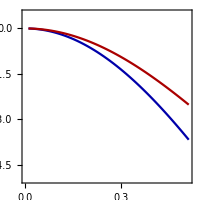
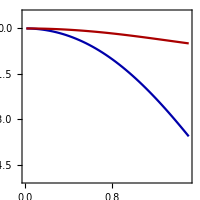
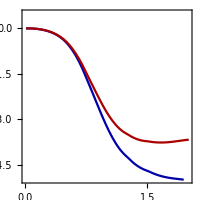
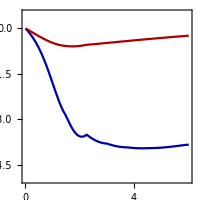
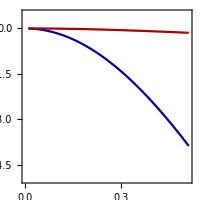
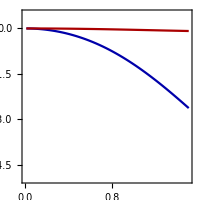
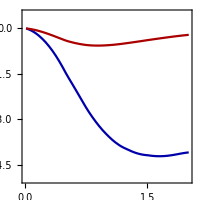
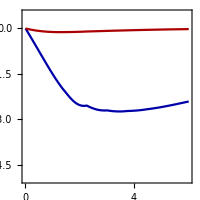
| -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  |  | -Graphics- |

```mathematica
SetOptions[MaTeX,Magnification->1.2];
SetOptions[Plot,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->12},PlotRange->{-5,0.5},PlotStyle->{Darker[Blue],Darker[Red]},Frame->True,FrameStyle->Black,ImageSize->200];
padding={{45,4},{12,8}};
PTrange[i_]:={PT,bin[i][[4,1]],bin[i][[4,2]]}
leftonly={Automatic,Directive[FontOpacity->0,FontSize->0]};
noticks=Directive[FontOpacity->0,FontSize->0];
leftandbottom=Automatic;
bottomonly={Directive[FontOpacity->0,FontSize->0],Automatic};
ticksArray[i_]:={leftonly,leftonly,leftonly,leftonly,leftandbottom,leftandbottom,leftandbottom,leftandbottom}[[i]]
Clear[p]
p[i_]:=Plot[{asymmetryNoFragU[i],asymmetryYesFragU[i]},PTrange[i],FrameTicksStyle->ticksArray[i],ImagePadding->padding]
grid=Grid[{{"",MaTeX["\\; \\; \\; \\; z\\in[0.1,0.4], \\; Q\\in[10,30]"],MaTeX["\\; \\; \\; \\; z\\in[0.1,0.4], \\; Q\\in[30,50]"],MaTeX["\\; \\; \\; \\; z\\in[0.4,0.8], \\; Q\\in[10,30]"],MaTeX["\\; \\; \\; \\; z\\in[0.4,0.8], \\; Q\\in[30,50]"],""},{Rotate[MaTeX["\\lambda_\\theta"],90Degree],p[1],p[2],p[3],p[4],Rotate[MaTeX["x\\in[0.1,0.5]"],-90Degree]},{Rotate[MaTeX["\\lambda_\\theta"],90Degree],p[5],p[6],p[7],p[8],Rotate[MaTeX["x\\in[0.5,1.0]"],-90Degree]},{"","","","",MaTeX["\\; \\; \\; \\;  {\\bf P}_\\perp \\; \\rm [GeV]"],""}},Spacings->{0,0}]
```

```mathematica
legend=LineLegend[{Darker[Blue],Darker[Red]},{MaTeX["{\\rm No \\; fragmentation}"],MaTeX["{\\rm Fragmentation}"]},LegendLayout->"Row"]
```

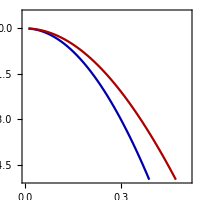
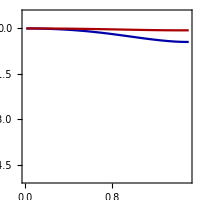
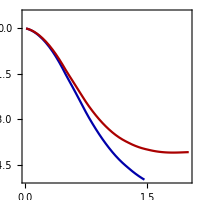
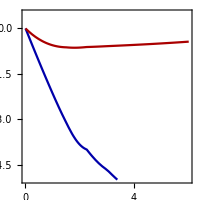
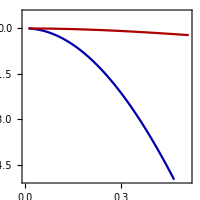
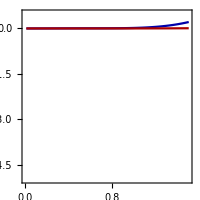
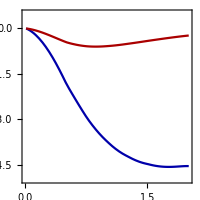
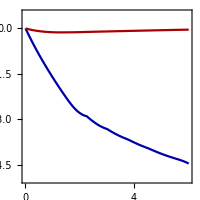
-Graphics-

 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  |  | -Graphics- |

```mathematica
fig=Grid[{{MaTeX["A_{\\cos{2\\phi}},\\; \\sqrt{s}=63 \\; \\rm GeV"]},{legend},{grid}}]
```

```mathematica
Export["/Users/reedhodges/Desktop/asymmetryU.pdf",fig]
```

/Users/reedhodges/Desktop/asymmetryU.pdf

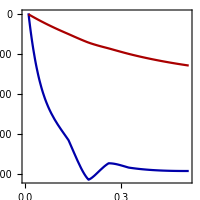
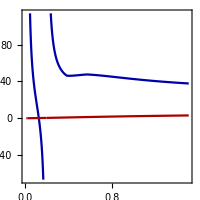
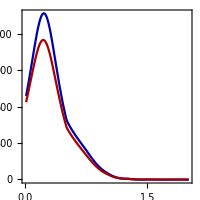
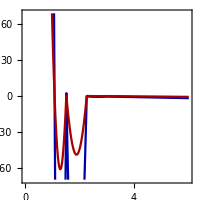
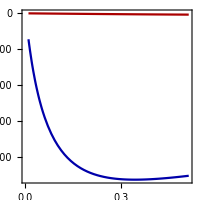
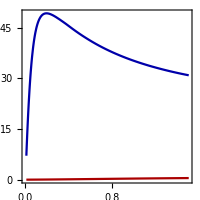
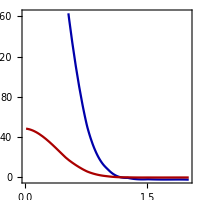
| -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  |  | -Graphics- |

```mathematica
SetOptions[MaTeX,Magnification->1.2];
SetOptions[Plot,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->12},PlotRange->Automatic,PlotStyle->{Darker[Blue],Darker[Red]},Frame->True,FrameStyle->Black,ImageSize->200];
padding={{45,4},{12,8}};
PTrange[i_]:={PT,bin[i][[4,1]],bin[i][[4,2]]}
leftonly={Automatic,Directive[FontOpacity->0,FontSize->0]};
noticks=Directive[FontOpacity->0,FontSize->0];
leftandbottom=Automatic;
bottomonly={Directive[FontOpacity->0,FontSize->0],Automatic};
ticksArray[i_]:={leftonly,leftonly,leftonly,leftonly,leftandbottom,leftandbottom,leftandbottom,leftandbottom}[[i]]
Clear[p]
p[i_]:=Plot[{asymmetryNoFragL[i],asymmetryYesFragL[i]},PTrange[i],FrameTicksStyle->ticksArray[i],ImagePadding->padding]
grid=Grid[{{"",MaTeX["\\; \\; \\; \\; z\\in[0.1,0.4], \\; Q\\in[10,30]"],MaTeX["\\; \\; \\; \\; z\\in[0.1,0.4], \\; Q\\in[30,50]"],MaTeX["\\; \\; \\; \\; z\\in[0.4,0.8], \\; Q\\in[10,30]"],MaTeX["\\; \\; \\; \\; z\\in[0.4,0.8], \\; Q\\in[30,50]"],""},{Rotate[MaTeX["\\lambda_\\theta"],90Degree],p[1],p[2],p[3],p[4],Rotate[MaTeX["x\\in[0.1,0.5]"],-90Degree]},{Rotate[MaTeX["\\lambda_\\theta"],90Degree],p[5],p[6],p[7],p[8],Rotate[MaTeX["x\\in[0.5,1.0]"],-90Degree]},{"","","","",MaTeX["\\; \\; \\; \\;  {\\bf P}_\\perp \\; \\rm [GeV]"],""}},Spacings->{0,0}]
```

```mathematica
legend=LineLegend[{Darker[Blue],Darker[Red]},{MaTeX["{\\rm No \\; fragmentation}"],MaTeX["{\\rm Fragmentation}"]},LegendLayout->"Row"]
```

```mathematica
fig=Grid[{{MaTeX["A_{\\cos{2\\phi}},\\; \\sqrt{s}=63 \\; \\rm GeV"]},{legend},{grid}}]
```

-Graphics-

 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  |  | -Graphics- |

```mathematica
Export["/Users/reedhodges/Desktop/asymmetryL.pdf",fig]
```

/Users/reedhodges/Desktop/asymmetryL.pdf